```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/youngsam/Code/SULI

## GOOD FITTINGS

```mathematica
Kann[a_]:=(
c={};
b=Import[a,"Table"]; (*confirmed: importing entire file*)
For[i=1,b[[i,2]]!="photon",i++,];
c=Take[b,i-1];
table={};
dane={}; (*dane = data*)
Δt={};
ΔF={};
(*NegativeDetected=0*)
Do[
If[Head[c[[i,1]]]==Real,{

time=c[[i,1]];
beta=c⟦i,5⟧;
z=c⟦i,6⟧;

If[time>0,
logtime=Log[10,time];
flux=c⟦i,2⟧;
fluxposerr=c⟦i,3⟧;
fluxnegerr=c⟦i,4⟧;

(*flux version*)
(*taking logs for flux*)
logflux=Log[10,c⟦i,2⟧];
logfluxerror=((c⟦i,3⟧+c⟦i,4⟧)/2)/(c[[i,2]]*Log[10]);
(*how to account for pos and neg error?*)
(*check if 1si or 2sig; 1sig = divide by 2, 2sig = divide by 2*1.65*)

If[flux>0,AppendTo[table,{logtime,logflux,logfluxerror}]];
If[flux>0,AppendTo[dane,{logtime,logflux}]];
If[flux>0,AppendTo[ΔF,logfluxerror]];
]}
]
,{i,1,Length[c]}];
)
```

```mathematica
Wczytywanie[a_]:=(
c={};
b=Import[a,"Table"]; (*confirmed: importing entire file*)
For[i=1,b[[i,2]]!="photon",i++,];
c=Take[b,i-1];
table={};
dane={}; (*dane = data*)
Δt={};
ΔF={};
(*NegativeDetected=0*)
Do[
If[Head[c[[i,1]]]==Real,{

beta=c⟦i,5⟧;
z=c⟦i,6⟧;
time=c[[i,1]]*(1+z);

If[time>0,
logtime=Log[10,time]; (*multiply by 1+z to get from rest to obs frame*)
flux=c⟦i,2⟧*((1+z)^(1-beta)); (*multiply by k-corr to get from rest->obs frame*)
fluxposerr=c⟦i,3⟧*((1+z)^(1-beta));
fluxnegerr=c⟦i,4⟧*((1+z)^(1-beta));

logflux=Log[10,flux];
logfluxerror=((fluxposerr+fluxnegerr)/2)/(flux*Log[10]);
If[flux>0,AppendTo[table,{logtime,logflux,logfluxerror}]];
If[flux>0,AppendTo[dane,{logtime,logflux}]];
If[flux>0,AppendTo[ΔF,logfluxerror]];
]}
]
,{i,1,Length[c]}];
)
```

```mathematica
(* use si if 3 columns *)
Si[a_]:=(
c={};
b=Import[a,"Table"]; (*confirmed: importing entire file*)
For[i=1,b[[i,2]]!="photon",i++,];
c=Take[b,i-1];
table={};
dane={}; (*dane = data*)
Δt={};
ΔF={};

Do[
If[Head[c[[i,1]]]==Real,{
time=c[[i,1]];
If[time>0,
logtime=Log[10,time];
flux=c⟦i,2⟧;
logflux=Log[10,c⟦i,2⟧];

logfluxerror=c⟦i,3⟧/(c[[i,2]]*Log[10]);(*check if 1si or 2sig; 1sig = divide by 2, 2sig = divide by 2*1.65*)


If[flux>0,AppendTo[table,{logtime,logflux,logfluxerror}]];
If[flux>0,AppendTo[dane,{logtime,logflux}]];
(*If[flux>0,AppendTo[Δt,logerrorontime]];*)
If[flux>0,AppendTo[ΔF,logfluxerror]];
]}
] 
,{i,1,Length[c]}];
)
```

```mathematica
Dzielenie[start_,end_]:= (*beginning of plateau emission, where you start and end the curve-fitting*)
(
Clear[counter];
startp=start ;
endp=end;
Part1={};
Δt1={};
ΔF1={};
Part2={};
Δt2={};
ΔF2={};
counter=0;

Do[If[startp≤dane[[i,1]]≤endp,
(
AppendTo[Part1,dane[[i]]];
AppendTo[Δt1,Δt[[i]]];
AppendTo[ΔF1,ΔF[[i]]];
counter=counter+1;
),
(
AppendTo[Part2,dane[[i]]];
AppendTo[Δt2,Δt[[i]]];
AppendTo[ΔF2,ΔF[[i]]];
)
],{i,1,Length[dane]}];

Print["number of points included: ",counter]
);
```

```mathematica
model[F_,T_,α_,t_]:=Piecewise[{{Log[10,10^F*Exp[α-(10^x*α/10^T)]*Exp[-Abs[t]/10^x]],10^x<10^T},{Log[10,10^F*(10^x/10^T)^(-α)*Exp[-Abs[t]/10^x]],10^x≥10^T}}];
```

```mathematica
(* a = F, b = T, c = alpha, d = t *)

fitowanie[a_,b_,c_,d_,er_,datapart_,beg_,end_]:=
(fit1=NonlinearModelFit[datapart,model[F,T,α,t],{{F,a},{T,b},{α,c},{t,d}},x,Weights->1/er^2];
bestparameters=fit1["BestFitParameters"];
besterrors=fit1["ParameterErrors"];
Print["----------------------------------------------"];
Print["best fit parameters: ",bestparameters];
Print["theirs errors: ",besterrors];
Print["confidence intervals: ",fit1["ParameterConfidenceIntervals",ConfidenceLevel->0.68]];


(*if Subscript[t, a] is <0 we have to fix it and refit in order for following Δχ^2 calculations*)
If[fit1["BestFitParameters"][[4,2]]≤0,
(
Clear[bestparameters];
startowe={{F,a},{T,b},{α,c}};
fit1=NonlinearModelFit[datapart,model[F,T,α,0],startowe,x,Weights->1/er^2]; (*this line has t=0*)
bestparameters=fit1["BestFitParameters"];
besterrors=fit1["ParameterErrors"];
zamiana[i_,k_]:={parametr[[i]]->FaTaTable[[i,k]],t->0};
start={{F,#[[1,2]]},{T,#[[2,2]]},{α,#[[3,2]]}}&[bestparameters];
Flux=model[F,T,α,0]/.bestparameters;
Print["!!!!!!!!!!!!!!!!!!! changing best fit parameters to: ",bestparameters," with fixed ta->0"];
Print["best fit parameters: ",bestparameters];
Print["theirs errors: ",besterrors];
Print["confidency intervals: ",fit1["ParameterConfidenceIntervals",ConfidenceLevel->0.68]];
),
(
zamiana[i_,k_]:={parametr[[i]]->FaTaTable[[i,k]]};
start={{F,#[[1,2]]},{T,#[[2,2]]},{α,#[[3,2]]},{t,#[[4,2]]}}&[bestparameters];
Flux=model[F,T,α,t]/.bestparameters
)
];
Print[
Show[
Plot[model[F,T,α,t]/.bestparameters/.t->0,{x,beg,end}],ListPlot[datapart,PlotRange->All],ListPlot[{{bestparameters[[2]][[2]],bestparameters[[1]][[2]]}},PlotStyle->{Green, PointSize[0.05]},PlotRange->All],
PlotRange->All,FrameLabel->{"log time rest frame (s)","log Flux (erg s^-1)"}]]
Print["----------------------------------------------"];
Clear[fit1];
)
```

```mathematica
Wycinanie[a_,b_]:=
(
przedziałT:=Interval[{a[[1]],b[[1]]}]; (*compartments = bins?*)
przedziałF:=Interval[{a[[2]],b[[2]]}];
Do[
If[!IntervalMemberQ[przedziałT,dane[[i,1]]]||!IntervalMemberQ[przedziałF,dane[[i,2]]],
(
AppendTo[Part12,dane[[i]]];
AppendTo[Δt12,Δt[[i]]];
AppendTo[ΔF12,ΔF[[i]]];
)
];
,{i,1,Length[dane]}];

dane=Part12;
Δt=Δt12;
ΔF=ΔF12;

Part12={};
Δt12={};
ΔF12={};
)
```

```mathematica
Chisquare[datapart_,er_]:=Module[{ν,REDUCED},


singleχ[j_]:=(1/er[[All]](datapart[[All,2]]-Flux/.x->datapart[[All,1]]))^2;

bestfitχ=Sum[singleχ[All],{All,1,Length[datapart]}];
REDUCED=bestfitχ/(Length[datapart]-3);
ν=Length[datapart];
X=REDUCED ν;
PROBABILITY=2^(-ν/2)/Gamma[ν/2] NIntegrate[ⅇ^(-x/2) x^(-1+ν/2),{x,X,Infinity}];
Print["GRB ",id," afterglow has"," χ^2: ",bestfitχ," and  reduced χ^2: ",REDUCED," α: ",Chop[PROBABILITY]];
];
```

```mathematica
IntervalEstimating[b_,e_,s_,datapart_,er_]:=
(
Print["--------------testing-------------"];
FaTaTable={};

parametr=Table[bestparameters[[i,1]],{i,1,3}];
bestparam=Table[bestparameters[[i,2]],{i,1,3}];
errors=Table[besterrors[[i]],{i,1,3}];

beg=b;                                             (*flexible interval for error multiplier*)
end=e;
step=s;
multiplier=Sort[Join[Table[-end+i step,{i,0,(end-beg)/step}],Table[beg+i step,{i,0,(end-beg)/step}]]];
Do[
values=Table[bestparam[[j]]+multiplier[[i]]*errors[[j]],{i,1,Length[multiplier]}];
AppendTo[FaTaTable,values]
,{j,1,3}];

quantity=2 ((end-beg)/step+1);

Print["---------------------------------"];

(*******  main ugly loop for Δχ^2 calculations :) ********)
Clear[Flux1];
singleχ[j_]:=((datapart[[j,2]]-Flux1/.x->datapart[[j,1]])/er[[j]])^2;
Δtable={{},{},{},{}};
finaltable={};
Print["---------------------------------"];
Do[

Do[
parametry=Drop[start,{i}];

fit12=NonlinearModelFit[datapart,model[F,T,α,t]/.zamiana[i,k],parametry,x,Weights->1/er^2];

Clear[χsquare,Flux1];
Flux1=model[F,T,α,t]/.fit12["BestFitParameters"]/.zamiana[i,k];
χsquare=Sum[singleχ[j],{j,1,Length[datapart]}];
Δχ=χsquare-bestfitχ;

AppendTo[Δtable[[i]],{multiplier[[k]],Chop[Δχ]}];

(*Print[Row[{"σ x ",multiplier[[k]],"   ","Δχ:",Chop[Δχ],"   ",zamiana[i,k],"  ",χsquare," ",fit12["BestFitParameters"]}]] ;*)
(*checking tool{set "i" for one value}*)
,{k,1,quantity}];


Clear[left,right,leftm,rightm];
left=Drop[Δtable[[i]],(-Length[Δtable[[i]]])/2];
right=Drop[Δtable[[i]],Length[Δtable[[i]]]/2];

Do[
(*Print[left[[t,2]],">3.5>",left[[t+1,2]]," ",left[[t,2]]≥3.5≥left[[t+1,2]]];*)
If[left[[t,2]]≥1≥left[[t+1,2]],leftm=((left[[t+1,1]]-left[[t,1]])(1-left[[t,2]]))/(left[[t+1,2]]-left[[t,2]])-left[[t,1]]];
If[right[[t,2]]≤1≤right[[t+1,2]],rightm=((right[[t+1,1]]-right[[t,1]])(1-right[[t,2]]))/(right[[t+1,2]]-right[[t,2]])-right[[t,1]]];
,{t,1,Length[Δtable[[i]]]/2-1}];
Print[leftm," ",rightm];
AppendTo[finaltable,
{bestparameters[[i,1]],
bestparameters[[i,2]],
(Sort[{If[NumericQ[leftm],bestparameters[[i,2]]+leftm besterrors[[i]],"error"],If[NumericQ[rightm],bestparameters[[i,2]]+rightm besterrors[[i]],"error"]}])}];

Clear[leftm,rightm];
,{i,1,3}];
(*parameters*)

Print[
TableForm[
Table[{finaltable[[i,1]],finaltable[[i,2]],"("<>ToString[finaltable[[i,3,1]]]<>" ,",ToString[finaltable[[i,3,2]]]<>")"},{i,1,3}]
,TableHeadings->{None,{"parameter","best fit"," confidency","interval"}}]];

Print[Row[Table[ListPlot[Δtable[[i]],PlotRange->All,ImageSize->Medium,PlotLabel->ToString[parametr[[i]]],FrameLabel->{"σ multiplier","Δχ^2"},Axes->False,Frame->True]
,{i,1,3}]]];

Print["---------------------------------"];
);
```

## FEBRURARY TXT 2021

```mathematica
(*Keep, even though high chi sq, check for plateau-Dainotti Checked*)
```

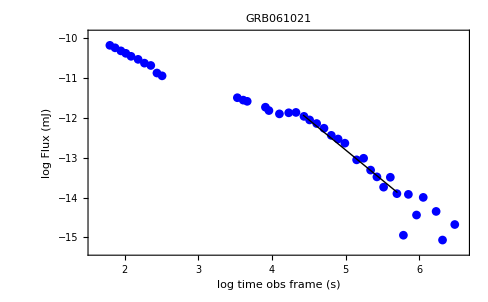
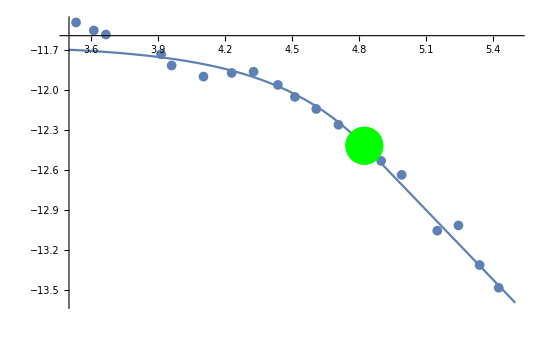
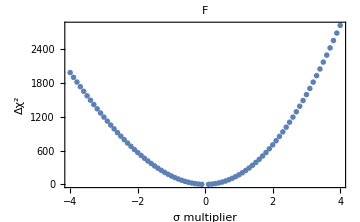
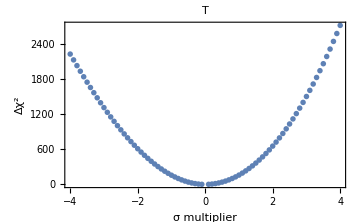
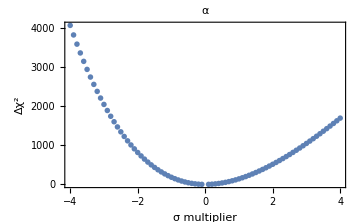
```mathematica
Si["GRB061021_Oates_ergs_Rband_hostextcorr.txt"]
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time obs frame (s)","log Flux (mJ)"},PlotLabel->"GRB061021"]

tt=3.9   (*start time of plateau, log scale*)
tf=5.68  (*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-11.95,4.43,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
-Graphics-
3.5
5.5
Part::partw: "Part \!\(\*RowBox[{\"1\"}]\) of \!\(\*RowBox[{\"{\", \"}\"}]\) does not exist."
Part::partw: "Part \!\(\*RowBox[{\"2\"}]\) of \!\(\*RowBox[{\"{\", \"}\"}]\) does not exist."
Part::partw: "Part \!\(\*RowBox[{\"3\"}]\) of \!\(\*RowBox[{\"{\", \"}\"}]\) does not exist."
General::stop: "Further output of \!\(\*StyleBox[RowBox[{\"Part\", \"::\", \"partw\"}], \"MessageName\"]\) will be suppressed during this calculation."
"number of points included: "19
NonlinearModelFit::sszero: "The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum."
"----------------------------------------------"
"best fit parameters: "{F->-12.29164702586769,T->4.676194442254981,α->1.5333616675187476,t->-3.078615137151016*^-9}
"theirs errors: "{0.1341754661089324,0.11369864600688244,0.10007808659083672,2534.4090451503903}
"confidence intervals: "{{-12.429650899397595,-12.153643152337784},{4.559251650706812,4.79313723380315},{1.430428068661085,1.63629526637641},{-2606.7229388749734,2606.722938868816}}
"!!!!!!!!!!!!!!!!!!! changing best fit parameters to: "{F->-12.419490986458799,T->4.823673140093301,α->1.736350998143708}" with fixed ta->0"
"best fit parameters: "{F->-12.419490986458799,T->4.823673140093301,α->1.736350998143708}
"theirs errors: "{0.06596302757208315,0.06576159215946277,0.10564616346344652}
"confidency intervals: "{{-12.487191293158409,-12.351790679759189},{4.756179574043969,4.8911667061426325},{1.6279224142631916,1.8447795820242243}}
-Graphics-
"----------------------------------------------"
NIntegrate::izero: "Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option."
"GRB "id" afterglow has"" \!\(\*SuperscriptBox[\(χ\), \(2\)]\): "2995.3160805778502" and  reduced \!\(\*SuperscriptBox[\(χ\), \(2\)]\): "187.20725503611564" α: "0
"--------------testing-------------"
"---------------------------------"
"---------------------------------"
NonlinearModelFit::sszero: "The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum."
NonlinearModelFit::sszero: "The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum."
NonlinearModelFit::sszero: "The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum."
General::stop: "Further output of \!\(\*StyleBox[RowBox[{\"NonlinearModelFit\", \"::\", \"sszero\"}], \"MessageName\"]\) will be suppressed during this calculation."
leftm" "rightm
leftm" "rightm
leftm" "rightm
{{"parameter", "best fit", " confidency", "interval"}, {F, -12.419490986458799, "(error ,", "error)"}, {T, 4.823673140093301, "(error ,", "error)"}, {α, 1.736350998143708, "(error ,", "error)"}}
-Graphics--Graphics--Graphics-
"---------------------------------"
```

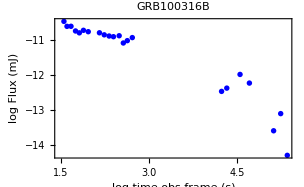
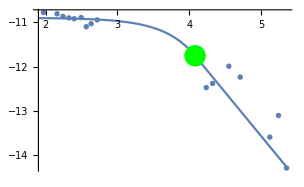
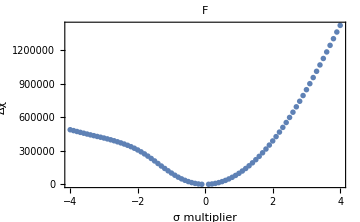
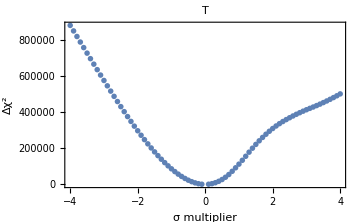
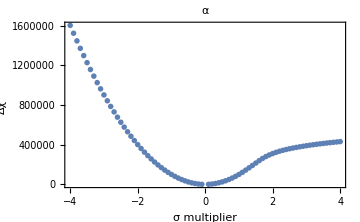
```mathematica
(*Delta chi sq not working due to a high variation and high chi sq, Keep-Dainotti checked*)
Si["GRB100316B_Oates_ergs_Rband_hostextcorr.txt"]
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time obs frame (s)","log Flux (mJ)"},PlotLabel->"GRB100316B"]

tt=1.9   (*start time of plateau, log scale*)
tf=5.36  (*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-10.9,2.71,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
Part::partw: "Part \!\(\*RowBox[{\"25\"}]\) of \!\(\*RowBox[{\"{\", RowBox[{RowBox[{\"{\", RowBox[{\"35.9782`\", \",\", \"2.2927`\", \",\", \"3.274920467069629`*^-11\", \",\", \"1.09246980305191`*^-11\", \",\", RowBox[{\"-\", \"1.0338831488115485`*^-11\"}], \",\", \"1.18`\", \",\", \"0.886`\"}], \"}\"}], \",\", RowBox[{\"{\", RowBox[{\"40.5685`\", \",\", \"2.2927`\", \",\", \"2.36569854572665`*^-11\", \",\", \"8.03695634611852`*^-12\", \",\", RowBox[{\"-\", \"7.621813078290514`*^-12\"}], \",\", \"1.18`\", \",\", \"0.886`\"}], \"}\"}], \",\", RowBox[{\"«\", \"20\", \"»\"}], \",\", RowBox[{\"{\", RowBox[{\"226408.3676`\", \",\", \"22607.8856`\", \",\", \"5.191026843408831`*^-15\", \",\", \"2.7744692525381105`*^-14\", \",\", RowBox[{\"-\", \"2.7739048622294236`*^-14\"}], \",\", \"1.18`\", \",\", \"0.886`\"}], \"}\"}], \",\", RowBox[{\"{\", RowBox[{\"274583.3611`\", \",\", \"25565.787`\", \",\", RowBox[{\"-\", \"3.659020350398989`*^-14\"}], \",\", \"3.2400484325720776`*^-14\", \",\", RowBox[{\"-\", \"3.215960535433715`*^-14\"}], \",\", \"1.18`\", \",\", \"0.886`\"}], \"}\"}]}], \"}\"}]\) does not exist."
-Graphics-
1.9
5.36
Part::partw: "Part \!\(\*RowBox[{\"1\"}]\) of \!\(\*RowBox[{\"{\", \"}\"}]\) does not exist."
Part::partw: "Part \!\(\*RowBox[{\"2\"}]\) of \!\(\*RowBox[{\"{\", \"}\"}]\) does not exist."
Part::partw: "Part \!\(\*RowBox[{\"3\"}]\) of \!\(\*RowBox[{\"{\", \"}\"}]\) does not exist."
General::stop: "Further output of \!\(\*StyleBox[RowBox[{\"Part\", \"::\", \"partw\"}], \"MessageName\"]\) will be suppressed during this calculation."
"number of points included: "16
NonlinearModelFit::sszero: "The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum."
"----------------------------------------------"
"best fit parameters: "{F->-11.873067445738382,T->4.142583671143888,α->1.968238366038908,t->-5.49299261747633*^-10}
"theirs errors: "{0.5489317406949988,0.31516150981153407,0.19019621972917858,249.5910391587946}
"confidence intervals: "{{-12.442532139308462,-11.303602752168302},{3.8156334525562747,4.469533889731501},{1.7709278008871578,2.165548931190658},{-258.9270652353756,258.92706523427705}}
"!!!!!!!!!!!!!!!!!!! changing best fit parameters to: "{F->-11.754221319393292,T->4.081453334635202,α->1.9679137536378193}" with fixed ta->0"
"best fit parameters: "{F->-11.754221319393292,T->4.081453334635202,α->1.9679137536378193}
"theirs errors: "{0.26222459858358216,0.19980883124785015,0.18112300398548242}
"confidency intervals: "{{-12.025355198511631,-11.483087440274952},{3.874855846104532,4.2880508231658725},{1.780636957588126,2.1551905496875126}}
-Graphics-
"----------------------------------------------"
NIntegrate::izero: "Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option."
"GRB "id" afterglow has"" \!\(\*SuperscriptBox[\(χ\), \(2\)]\): "1.3076315196534288*^6" and  reduced \!\(\*SuperscriptBox[\(χ\), \(2\)]\): "100587.03997334068" α: "0
"--------------testing-------------"
"---------------------------------"
"---------------------------------"
leftm" "rightm
leftm" "rightm
leftm" "rightm
{{"parameter", "best fit", " confidency", "interval"}, {F, -11.754221319393292, "(error ,", "error)"}, {T, 4.081453334635202, "(error ,", "error)"}, {α, 1.9679137536378193, "(error ,", "error)"}}
-Graphics--Graphics--Graphics-
"---------------------------------"
```

```mathematica
ALL 57 LCS DISCARD RECOVER PL
```

```mathematica
(*Confirm Recover-Dainotti checked*)
```

Part::partw: Part 11 of {{5185.4,1.16264×10^-12,1.68506×10^-13,1.97067×10^-13,0.6,0.671},{6480.,1.35222×10^-12,2.27492×10^-13,2.73505×10^-13,0.6,0.671},{7920.,2.57659×10^-12,4.33476×10^-13,5.21153×10^-13,0.6,0.671},{32115.,1.19082×10^-12,2.87491×10^-13,3.78986×10^-13,0.6,0.671},{86850.,4.06861×10^-13,1.25382×10^-13,1.81232×10^-13,0.6,0.671},{90615.,3.97234×10^-13,6.68291×10^-14,8.03462×10^-14,0.6,0.671},{91215.,3.976×10^-13,9.59895×10^-14,1.26539×10^-13,0.6,0.671},{119750.,1.91182×10^-13,1.68219×10^-14,1.84449×10^-14,0.6,0.671},{173250.,7.03147×10^-14,1.18295×10^-14,1.42222×10^-14,0.6,0.671},{177015.,7.03795×10^-14,1.69912×10^-14,2.23987×10^-14,0.6,0.671}} does not exist.

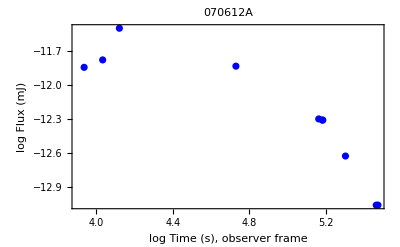

3.9

5.47

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 9

----------------------------------------------

best fit parameters: {F→-12.376,T→5.2145,α→2.69428,t→10881.4}

theirs errors: {0.320531,0.131631,0.481785,4748.48}

confidence intervals: {{-12.7297,-12.0222},{5.06922,5.35978},{2.16255,3.22601},{5640.7,16122.2}}

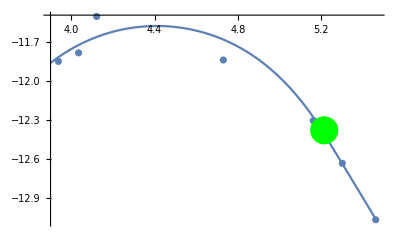

----------------------------------------------

GRB id afterglow has χ^2: 6.37075 and  reduced χ^2: 1.06179 α: 0.387599

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

1.13808 -0.86911

1.18064 -0.845077

0.988574 -1.03049

parameter | best fit |  confidency | interval
F | -12.376 | (-12.6545 , | -12.0112)
T | 5.2145 | (5.10326 , | 5.36991)
α | 2.69428 | (2.1978 , | 3.17056)

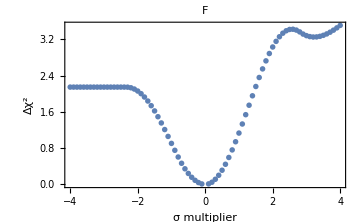
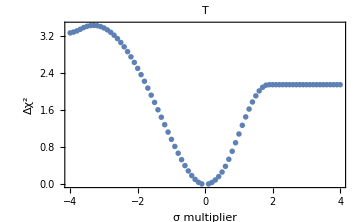
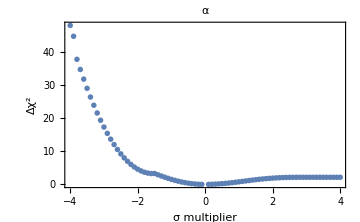

---------------------------------

```mathematica
Wczytywanie["070612A_block1_ergs.txt"]
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log Time (s), observer frame","log Flux (mJ)"},PlotLabel->"070612A"]

tt=3.9   (*start time of plateau, log scale*)
tf=5.47  (*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-12.31,5.18,1.5,0,ΔF1,Part1,tt,tf] (*flux at end of plateau, time at end of plateau*)
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

```mathematica
(*Confirm Recover-Dainotti checked*)
```

Part::partw: Part 502 of {{56.0131,6.65675×10^-11,4.15634×10^-12,4.43314×10^-12,0.60705,0.971},{79.2547,4.5327×10^-11,2.59526×10^-12,2.57599×10^-12,0.60705,0.971},{89.2771,4.14904×10^-11,2.23123×10^-12,2.23698×10^-12,0.60705,0.971},{99.2995,3.75262×10^-11,1.91983×10^-12,1.91415×10^-12,0.60705,0.971},«44»,{6605.91,5.74362×10^-13,9.79468×10^-14,9.7973×10^-14,0.60705,0.971},{6811.08,6.7241×10^-13,8.40621×10^-14,8.41339×10^-14,0.60705,0.971},«451»} does not exist.

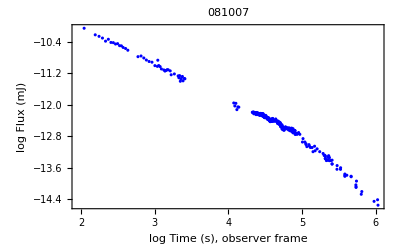

3.6

5.5

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 439

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

----------------------------------------------

best fit parameters: {F→-12.6498,T→4.83198,α→1.46882,t→-6.00348×10^-9}

theirs errors: {0.029596,0.0204527,0.0241195,5260.47}

confidence intervals: {{-12.6793,-12.6203},{4.81162,4.85234},{1.44481,1.49284},{-5237.31,5237.31}}

!!!!!!!!!!!!!!!!!!! changing best fit parameters to: {F→-12.4751,T→4.65931,α→1.2451} with fixed ta->0

best fit parameters: {F→-12.4751,T→4.65931,α→1.2451}

theirs errors: {0.00935586,0.00936046,0.0125368}

confidency intervals: {{-12.4844,-12.4658},{4.64999,4.66863},{1.23262,1.25759}}

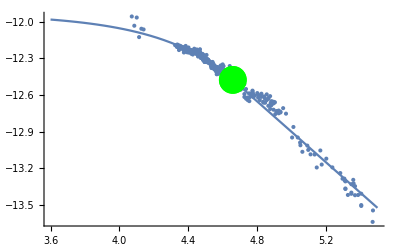

----------------------------------------------

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

GRB id afterglow has χ^2: 1489.79 and  reduced χ^2: 3.41695 α: 0

--------------testing-------------

---------------------------------

---------------------------------

0.727353 -0.536833

0.734334 -0.524864

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

0.78312 -0.570194

parameter | best fit |  confidency | interval
F | -12.4751 | (-12.4801 , | -12.4683)
T | 4.65931 | (4.65439 , | 4.66618)
α | 1.2451 | (1.23796 , | 1.25492)

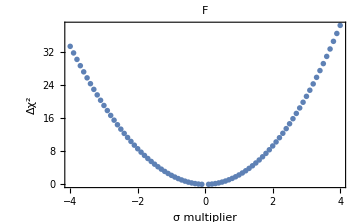
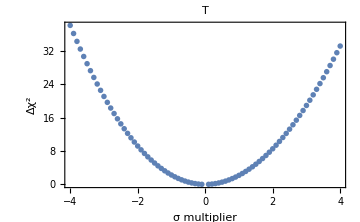
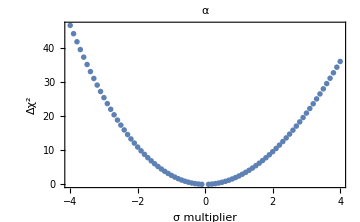

---------------------------------

```mathematica
Wczytywanie["091018_block1_ergs.txt"] (*Check again*)
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log Time (s), observer frame","log Flux (mJ)"},PlotLabel->"081007"]

tt=3.6 (*start time of plateau, log scale*)
tf=5.5(*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-12.63,4.88,1.5,0,ΔF1,Part1,tt,tf] (*flux at end of plateau, time at end of plateau*)
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

```mathematica
(*Confirm Recover-Dainotti checked*)(*Confirm for peak*)
```

Part::partw: Part 369 of {{77.5613,5.38612×10^-12,4.28629×10^-13,4.65689×10^-13,0.69,0.71627},{104.639,4.57557×10^-12,3.29079×10^-13,3.54581×10^-13,0.69,0.71627},{127.768,2.15288×10^-12,2.76326×10^-13,3.17016×10^-13,0.69,0.71627},{151.589,1.84055×10^-12,2.30347×10^-13,2.63299×10^-13,0.69,0.71627},«44»,{588.194,2.27533×10^-12,1.63717×10^-13,1.7641×10^-13,0.69,0.71627},{599.124,2.31126×10^-12,5.2582×10^-13,6.80677×10^-13,0.69,0.71627},«318»} does not exist.

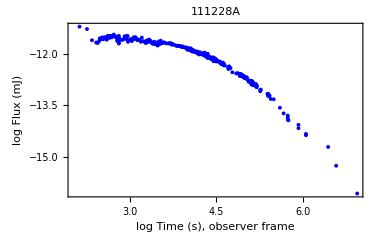

2.38

5.3

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 343

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

----------------------------------------------

best fit parameters: {F→-12.0432,T→4.32364,α→0.950689,t→-2.71851×10^-10}

theirs errors: {0.00709042,0.0100622,0.00606134,18.6301}

confidence intervals: {{-12.0502,-12.0361},{4.31362,4.33366},{0.944652,0.956725},{-18.554,18.554}}

!!!!!!!!!!!!!!!!!!! changing best fit parameters to: {F→-12.0111,T→4.28017,α→0.93593} with fixed ta->0

best fit parameters: {F→-12.0111,T→4.28017,α→0.93593}

theirs errors: {0.00578164,0.00877073,0.00536698}

confidency intervals: {{-12.0169,-12.0054},{4.27144,4.28891},{0.930585,0.941275}}

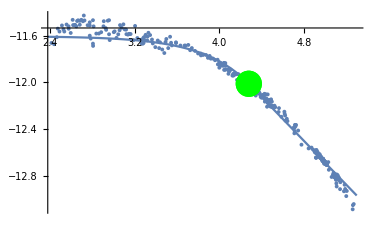

----------------------------------------------

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

GRB id afterglow has χ^2: 1522.25 and  reduced χ^2: 4.47721 α: 0

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

0.654788 -0.452659

0.646544 -0.449164

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

0.674638 -0.47158

parameter | best fit |  confidency | interval
F | -12.0111 | (-12.0137 , | -12.0073)
T | 4.28017 | (4.27623 , | 4.28584)
α | 0.93593 | (0.933399 , | 0.93955)

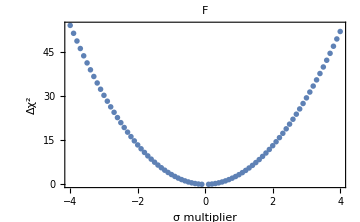
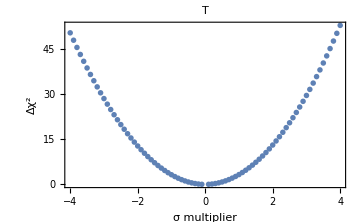
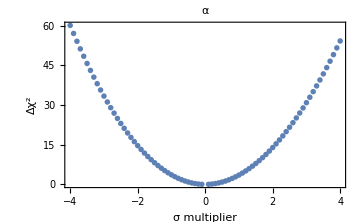

---------------------------------

```mathematica
Wczytywanie["111228A_block1_ergs.txt"] 
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log Time (s), observer frame","log Flux (mJ)"},PlotLabel->"111228A"]

tt=2.38  (*start time of plateau, log scale*)
tf=5.3  (*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-12,4.3,1.5,0,ΔF1,Part1,tt,tf] (*flux at end of plateau, time at end of plateau*)
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

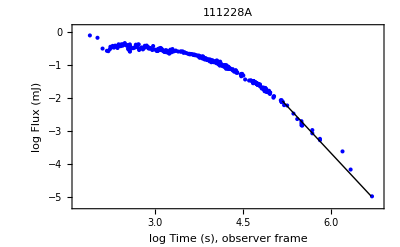

2.6

5.2

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 315

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

----------------------------------------------

best fit parameters: {F→-1.00443,T→4.14514,α→0.976969,t→-6.05638×10^-9}

theirs errors: {0.0102053,0.0129564,0.00763113,179.361}

confidence intervals: {{-1.0146,-0.994267},{4.13224,4.15805},{0.969368,0.98457},{-178.653,178.653}}

!!!!!!!!!!!!!!!!!!! changing best fit parameters to: {F→-0.944623,T→4.06651,α→0.949515} with fixed ta->0

best fit parameters: {F→-0.944623,T→4.06651,α→0.949515}

theirs errors: {0.00614539,0.00920646,0.00580482}

confidency intervals: {{-0.950744,-0.938502},{4.05734,4.07568},{0.943733,0.955297}}

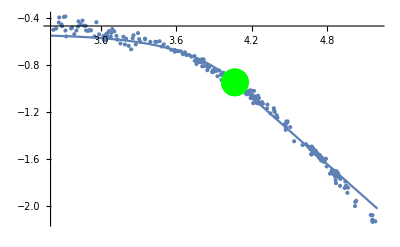

----------------------------------------------

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

GRB id afterglow has χ^2: 1516.4 and  reduced χ^2: 4.86026 α: 0

--------------testing-------------

---------------------------------

---------------------------------

0.678901 -0.476968

0.671859 -0.474241

0.695962 -0.493026

parameter | best fit |  confidency | interval
F | -0.944623 | (-0.947554 , | -0.940451)
T | 4.06651 | (4.06215 , | 4.0727)
α | 0.949515 | (0.946653 , | 0.953555)

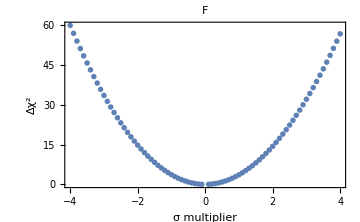
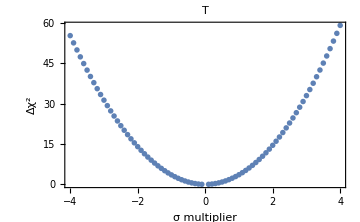
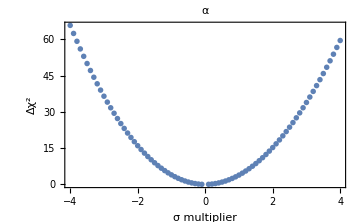

---------------------------------

```mathematica
(*Confirm Recover-Dainotti checked*)
```

Part::partw: Part 20 of {{5499.61,9.65618×10^-15,4.346×10^-16,4.55082×10^-16,0.53989,7.84},{6088.83,9.8943×10^-15,1.51158×10^-15,1.78415×10^-15,0.53989,7.84},{8183.46,8.59887×10^-15,1.04027×10^-15,1.18344×10^-15,0.53989,7.84},{10089.,8.33307×10^-15,1.71388×10^-15,2.15764×10^-15,0.53989,7.84},{11943.3,6.22933×10^-15,4.95546×10^-16,5.38374×10^-16,0.53989,7.84},«9»,{370967.,3.82054×10^-16,3.99764×10^-17,4.46481×10^-17,0.53989,7.84},{445819.,2.3449×10^-16,2.83681×10^-17,3.22723×10^-17,0.53989,7.84},{569309.,1.98667×10^-16,3.1894×10^-17,3.79934×10^-17,0.53989,7.84},{640843.,1.30054×10^-16,2.28716×10^-17,2.77522×10^-17,0.53989,7.84},{1.72152×10^6,6.2248×10^-17,0.,0.,0.53989,7.84}} does not exist.

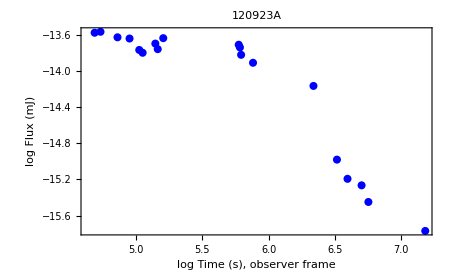

4.68

7.18

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 18

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

----------------------------------------------

best fit parameters: {F→-14.208,T→5.97041,α→1.42797,t→-22.6288}

theirs errors: {0.212798,0.261717,0.298314,14783.4}

confidence intervals: {{-14.4274,-13.9886},{5.70057,6.24026},{1.1204,1.73555},{-15265.1,15219.9}}

!!!!!!!!!!!!!!!!!!! changing best fit parameters to: {F→-14.618,T→6.37724,α→2.31157} with fixed ta->0

best fit parameters: {F→-14.618,T→6.37724,α→2.31157}

theirs errors: {0.234332,0.151065,0.525059}

confidency intervals: {{-14.8591,-14.377},{6.22187,6.53262},{1.77153,2.85161}}

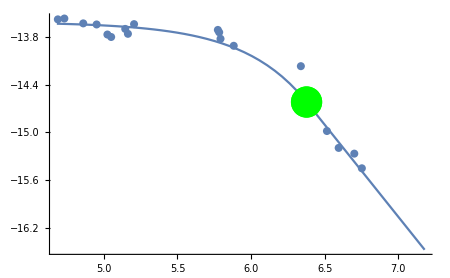

----------------------------------------------

GRB id afterglow has χ^2: 45.6714 and  reduced χ^2: 3.04476 α: 0.0000137343

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

0.543179 -0.374323

0.534814 -0.38603

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

0.575728 -0.340086

parameter | best fit |  confidency | interval
F | -14.618 | (-14.7058 , | -14.4908)
T | 6.37724 | (6.31893 , | 6.45803)
α | 2.31157 | (2.13301 , | 2.61386)

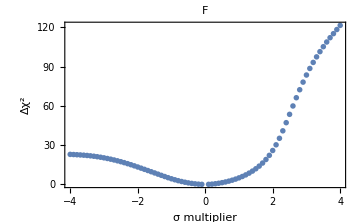
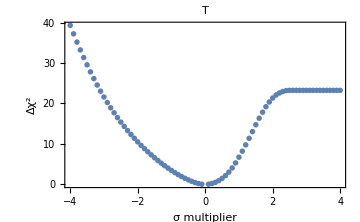
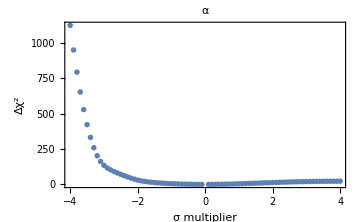

---------------------------------

```mathematica
Wczytywanie["120923A_block1_ergs.txt"] 
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log Time (s), observer frame","log Flux (mJ)"},PlotLabel->"120923A"]

tt=4.68 (*start time of plateau, log scale*)
tf=7.18  (*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-13.89,5.88,1.5,0,ΔF1,Part1,tt,tf] (*flux at end of plateau, time at end of plateau*)
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

```mathematica
(*Confirm Recover, remove flare-Dainotti checked*)
```

Part::partw: Part 27 of {{222.497,2.48713×10^-13,9.17859×10^-14,1.45471×10^-13,0.61,4.954},{260.004,1.88668×10^-13,4.55488×10^-14,6.0045×10^-14,0.61,4.954},{417.217,3.595×10^-13,8.67914×10^-14,1.14413×10^-13,0.61,4.954},{767.353,6.85014×10^-13,1.65378×10^-13,2.1801×10^-13,0.61,4.954},{1775.02,1.78525×10^-13,1.57083×10^-14,1.72238×10^-14,0.61,4.954},«17»,{40722.5,1.50395×10^-14,2.10742×10^-15,2.45085×10^-15,0.61,4.954},{40722.5,1.48807×10^-14,2.07567×10^-15,2.41214×10^-15,0.61,4.954},{56497.,1.45051×10^-14,5.44414×10^-16,5.44414×10^-16,0.61,4.954},{100596.,7.54347×10^-15,5.3584×10^-16,5.76813×10^-16,0.61,4.954}} does not exist.

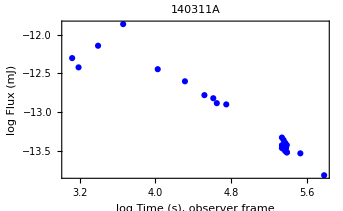

3.18

5.78

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 25

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

----------------------------------------------

best fit parameters: {F→-12.1006,T→3.72216,α→0.813814,t→-1644.39}

theirs errors: {0.755901,0.845858,0.0459212,2118.72}

confidence intervals: {{-12.8705,-11.3306},{2.86059,4.58372},{0.76704,0.860588},{-3802.45,513.671}}

!!!!!!!!!!!!!!!!!!! changing best fit parameters to: {F→-12.4728,T→4.12315,α→0.78059} with fixed ta->0

best fit parameters: {F→-12.4728,T→4.12315,α→0.78059}

theirs errors: {0.110994,0.162791,0.027368}

confidency intervals: {{-12.5858,-12.3599},{3.95752,4.28878},{0.752744,0.808435}}

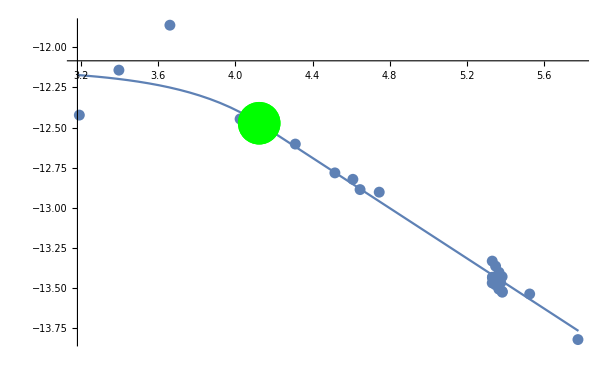

----------------------------------------------

GRB id afterglow has χ^2: 35.8059 and  reduced χ^2: 1.62754 α: 0.0247486

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

0.978249 -0.936358

1.16761 -0.759897

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

0.989246 -0.723251

parameter | best fit |  confidency | interval
F | -12.4728 | (-12.5768 , | -12.3643)
T | 4.12315 | (3.99944 , | 4.31322)
α | 0.78059 | (0.760796 , | 0.807664)

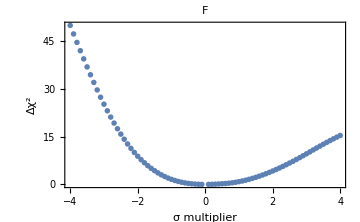
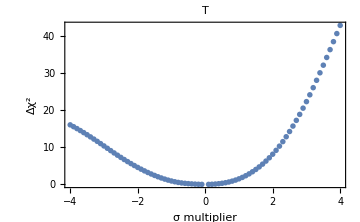
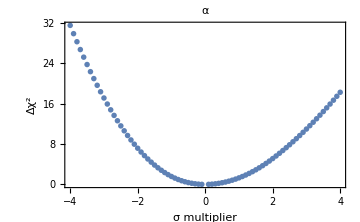

---------------------------------

```mathematica
Wczytywanie["140311A_block1_ergs.txt"] 
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log Time (s), observer frame","log Flux (mJ)"},PlotLabel->"140311A"]

tt=3.18 (*start time of plateau, log scale*)
tf=5.78  (*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-12.44,4.02,1.5,0,ΔF1,Part1,tt,tf] (*flux at end of plateau, time at end of plateau*)
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

```mathematica
(*Confirm Recover-Dainotti approved*
```

```mathematica
Si["/Users/youngsam/Code/SULI/gcn_circular_crawler_data/additional_subaru/010222/010222_nonsubaru_magnitudes_ready_for_conversion_flux_R.txt"](*Check again*)
nonsub = ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,PlotMarkers->{"•"},LabelStyle->{"Symbol",Black,18},FrameLabel->{"log Time (s)","log Flux (erg cm^-2 s^-1)"},PlotLabel->"010222", ImageSize->Large,FrameStyle->Directive[Thin,Black],PlotLegends->Placed[LineLegend[{"Other + Swift"},LegendMarkers->Automatic,Spacings->0.15],Scaled[{.85,.92}]]];
Si["/Users/youngsam/Code/SULI/gcn_circular_crawler_data/additional_subaru/010222/GRB010222_Watanabe_Subaru_format_for_conversion_flux_R.txt"]
sub = ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Red,PlotMarkers->{"✶","•"},PlotLegends->Placed[LineLegend[{"SUBARU"},LegendMarkers->Automatic,Spacings->0.15],Scaled[{.82,.84}]],LabelStyle->{"Symbol",18},FrameLabel->{"log time obs frame (s)","log Flux (erg cm^-2 s^-1)"},PlotLabel->"010222",ImageSize->Large,FrameStyle->Directive[Thin,Black]];

Show[nonsub,sub]
```

Part::partw: Part 58 of {{time_sec,flux,flux_err,band},{166580.,5.41561×10^-14,1.49639×10^-15,R},{15380.4,5.51629×10^-13,2.99761×10^-14,R},{17454.,4.76044×10^-13,2.36765×10^-14,R},{18145.2,4.10816×10^-13,2.23242×10^-14,R},{19441.2,4.14617×10^-13,2.1767×10^-14,R},{48938.2,1.80987×10^-13,2.16704×10^-14,R},{56861.,1.62049×10^-13,2.23879×10^-14,R},{65215.9,1.31113×10^-13,2.05292×10^-14,R},{74175.6,1.10065×10^-13,3.14257×10^-14,R},«47»} does not exist.

Part::partw: Part 8 of {{time_sec,flux,flux_err,band},{16935.4,4.46732×10^-13,1.64582×10^-14,R},{17323.,4.46321×10^-13,1.23323×10^-14,R},{29153.1,3.1049×10^-13,1.08669×10^-14,R},{29859.9,3.08494×10^-13,1.19336×10^-14,R},{286928.,2.16594×10^-14,2.99236×10^-16,R},{288028.,2.41239×10^-14,7.11005×10^-16,R}} does not exist.

-Graphics-

```mathematica
Show[ErrorListPlot[table, PlotRange-> All]]
```

Show::gtype: ErrorListPlot is not a type of graphics.

Show[ErrorListPlot[{{4.22879,-12.35,0.016},{4.23862,-12.3504,0.012},{4.46469,-12.508,0.0152},{4.47509,-12.5108,0.0168},{5.45777,-13.6644,0.006},{5.45943,-13.6176,0.0128}},PlotRange→All]]

Show::gcomb: Could not combine the graphics objects in Show[ErrorListPlot[«1»],ErrorListPlot[{{4.22879,-12.35,0.016},{4.23862,-12.3504,0.012},{4.46469,-12.508,0.0152},{4.47509,-12.5108,0.0168},{5.45777,-13.6644,0.006},{5.45943,-13.6176,0.0128}},«6»,PlotLabel→GRB010222]].

Show[ErrorListPlot[{{5.22162,-13.2664,0.012},{4.18697,-12.2584,0.0236},{4.24189,-12.3224,0.0216},{4.25876,-12.3864,0.0236},{4.28872,-12.3824,0.0228},{4.64808,-12.4723,0.124},{4.68965,-12.7424,0.052},{4.72235,-12.5785,0.052},{4.75481,-12.7904,0.06},{4.78496,-12.6665,0.056},{4.81435,-12.8824,0.068},{4.85868,-12.8145,0.084},{4.87026,-12.9584,0.124},{4.19728,-11.9203,0.008},{4.94236,-12.6363,0.04},{4.99419,-12.9784,0.028},{5.73895,-13.9544,0.06},{4.78298,-12.8076,0.0056},{4.78723,-12.7972,0.0052},{4.78998,-12.81,0.0048},{4.82661,-12.846,0.0044},{4.82912,-12.8552,0.004},{4.85992,-12.8876,0.0036},{4.87006,-12.8984,0.0056},{4.8925,-12.9268,0.0036},{4.92677,-12.9648,0.0072},{5.18255,-13.2944,0.0096},{5.19738,-13.3044,0.0096},{5.19845,-13.3192,0.01},{5.19968,-13.3352,0.01},{5.20367,-13.3168,0.0092},{5.20766,-13.3316,0.01},{5.21028,-13.3144,0.0092},{5.22407,-13.3284,0.0088},{5.37512,-13.5288,0.0228},{5.37583,-13.4848,0.0232},{5.40567,-13.5696,0.0176},{5.40638,-13.5812,0.0164},{4.19037,-12.2704,0.02},{4.2712,-12.3184,0.02},{4.27019,-12.3824,0.024},{4.29921,-12.3784,0.024},{5.27,-13.4064,0.024},{4.78286,-12.7384,0.012},{4.78717,-12.7264,0.012},{4.78992,-12.7384,0.012},{4.82666,-12.7744,0.012},{4.82917,-12.7864,0.012},{4.86002,-12.8184,0.012},{4.87001,-12.8304,0.02},{5.73895,-13.9544,0.06},{5.19609,-12.9344,0.02},{5.43213,-13.5064,0.032},{4.74406,-12.7636,0.048},{4.13322,-12.1864,0.008},{4.15746,-12.1984,0.008},{4.2531,-12.2584,0.008},{5.73895,-14.0064,0.04},{5.80103,-14.0984,0.04},{5.85732,-14.1544,0.04},{4.87404,-12.3923,0.028},{4.8864,-12.8145,0.036},{4.7815,-12.8807,0.04},{4.87072,-13.1207,0.08},{4.81739,-12.9974,0.12},{4.9158,-12.8944,0.024},{4.91936,-12.6305,0.028},{4.9228,-12.9896,0.052},{4.92622,-12.8424,0.06}},PlotRange→All,Frame→True,Axes→False,RotateLabel→True,PlotStyle→RGBColor[0, 0, 1],FrameLabel→{log time obs frame (s),log Flux (erg cm^-2 s^-1)},PlotLabel→GRB010222],ErrorListPlot[{{4.22879,-12.35,0.016},{4.23862,-12.3504,0.012},{4.46469,-12.508,0.0152},{4.47509,-12.5108,0.0168},{5.45777,-13.6644,0.006},{5.45943,-13.6176,0.0128}},PlotRange→All,Frame→True,Axes→False,RotateLabel→True,PlotStyle→RGBColor[1, 0, 0],FrameLabel→{log time obs frame (s),log Flux (erg cm^-2 s^-1)},PlotLabel→GRB010222]]

Part::partw: Part 70 of {{166580.,5.41561×10^-14,1.49639×10^-15},{15380.4,5.51629×10^-13,2.99761×10^-14},{17454.,4.76044×10^-13,2.36765×10^-14},{18145.2,4.10816×10^-13,2.23242×10^-14},{19441.2,4.14617×10^-13,2.1767×10^-14},{44471.3,3.37019×10^-13,9.62258×10^-14},{48938.2,1.80987×10^-13,2.16704×10^-14},{52765.7,2.63915×10^-13,3.15997×10^-14},{56861.,1.62049×10^-13,2.23879×10^-14},{60947.8,2.15508×10^-13,2.77887×10^-14},«59»} does not exist.

Part::partw: Part 8 of {{time_sec,flux,flux_err,band},{16935.4,4.46732×10^-13,1.64582×10^-14,R},{17323.,4.46321×10^-13,1.23323×10^-14,R},{29153.1,3.1049×10^-13,1.08669×10^-14,R},{29859.9,3.08494×10^-13,1.19336×10^-14,R},{286928.,2.16594×10^-14,2.99236×10^-16,R},{288028.,2.41239×10^-14,7.11005×10^-16,R}} does not exist.

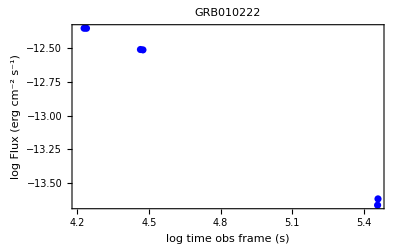

4.05

7.25

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 6

NonlinearModelFit::nrlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of real numbers with dimensions {6} at {F,T,α,t} = {-1000.26,663.097,1.36655,15426.8}.

General::munfl: 1/10^1000.26 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FittedModel::varnum: The estimated variance Indeterminate is not a positive number. Properties requiring division by the variance or standard error will not be computed.

Experimental`NumericalFunction::nnum: The function value Indeterminate is not a number at {F,T,α,t} = {-1000.26,663.097,1.36655,15426.8}.

General::stop: Further output of Experimental`NumericalFunction::nnum will be suppressed during this calculation.

SingularValueDecomposition::matrix: Argument {62.5 Experimental`NumericalFunction[{Hold[Piecewise[{{«2»},{«2»}},0]],Block},{0,{{{},1,0,Hold[F],0,0},{{},1,1,Hold[T],0,0},{{},1,2,Hold[α],0,0},{{},1,3,Hold[t],0,0}}},{{{1,4,817},{{Automatic,Automatic,None,1,Automatic,Automatic},{Automatic,Automatic,None,1,Automatic,Automatic}}}},{0,3,{},0},{904,MachinePrecision,{{Automatic},{Hold[Piecewise[«2»]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→(«1»&)},{},Automatic,WVM},Experimental`NumericalFunction,Automatic,None},{None,None,None}][Gradient[{-1000.26,663.097,1.36655,15426.8}]],«4»,78.125 Experimental`NumericalFunction[«1»][Gradient[{«1»}]]} at position 1 is not a non-empty rectangular matrix.

FittedModel::nosvd: Unable to obtain the singular value decomposition for the design matrix corresponding to the linearized problem. Some property values cannot be computed.

----------------------------------------------

best fit parameters: {F→-1000.26,T→663.097,α→1.36655,t→15426.8}

theirs errors: Missing[]

FittedModel::varnum: The estimated variance Indeterminate is not a positive number. Properties requiring division by the variance or standard error will not be computed.

SingularValueDecomposition::matrix: Argument {62.5 Experimental`NumericalFunction[{Hold[Piecewise[{{«2»},{«2»}},0]],Block},{0,{{{},1,0,Hold[F],0,0},{{},1,1,Hold[T],0,0},{{},1,2,Hold[α],0,0},{{},1,3,Hold[t],0,0}}},{{{1,4,817},{{Automatic,Automatic,None,1,Automatic,Automatic},{Automatic,Automatic,None,1,Automatic,Automatic}}}},{0,3,{},0},{904,MachinePrecision,{{Automatic},{Hold[Piecewise[«2»]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→(«1»&)},{},Automatic,WVM},Experimental`NumericalFunction,Automatic,None},{None,None,None}][Gradient[{-1000.26,663.097,1.36655,15426.8}]],«4»,78.125 Experimental`NumericalFunction[«1»][Gradient[{«1»}]]} at position 1 is not a non-empty rectangular matrix.

FittedModel::nosvd: Unable to obtain the singular value decomposition for the design matrix corresponding to the linearized problem. Some property values cannot be computed.

confidence intervals: Missing[]

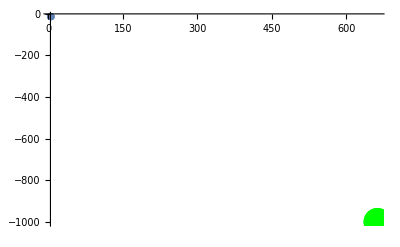

----------------------------------------------

NIntegrate::inumr: The integrand ⅇ^(-x/2) x^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,Indeterminate}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

GRB id afterglow has χ^2: Indeterminate and  reduced χ^2: Indeterminate α: 1/16 NIntegrate[ⅇ^(-x/2) x^(-1+ν$1407105/2),{x,X,∞}]

--------------testing-------------

Part::partw: Part 1 of Missing[] does not exist.

Part::partw: Part 2 of Missing[] does not exist.

Part::partw: Part 3 of Missing[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

General::munfl: 1/10^658.868 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/10^658.858 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/10^658.632 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {62.5 (12.35+0.434294 Log[1.57717 10.^Plus[«2»]]),83.3333 (12.3504+0.434294 Log[1.60964 10.^Plus[«2»]]),65.7895 (12.508+0.434294 Log[2.31032 10.^Plus[«2»]]),59.5238 (12.5108+0.434294 Log[2.33944 10.^Plus[«2»]]),166.667 (13.6644+0.434294 Log[3.71651 10.^Plus[«2»]]),78.125 (13.6176+0.434294 Log[3.71727 10.^Plus[«2»]])} is not a list of real numbers with dimensions {6} at {T,α,t} = {663.097,1.36655,15426.8}.

General::stop: Further output of NonlinearModelFit::nrlnum will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{{4.22879,-12.35},{4.23862,-12.3504},{4.46469,-12.508},{4.47509,-12.5108},{5.45777,-13.6644},{5.45943,-13.6176}},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,663.097},{α,1.36655},{t,15426.8}},x,Weights→{3906.25,6944.44,4328.25,3543.08,27777.8,6103.52}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

General::ivar: 4.22879 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

leftm rightm

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
F | -1000.26 | (error , | error)
T | 663.097 | (error , | error)
α | 1.36655 | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

```mathematica
Si["/Users/youngsam/Code/SULI/gcn_circular_crawler/manual_scraping/010222_all_data_flux_R.txt"]

tt=4.05   (*start time of plateau, log scale*)
tf=7.25  (*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-12.38,4.2,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,
ΔF1]
```

```mathematica
(*Confirm Recovered-Keep but compare with others discarded for a better chi sq- Dainotti approved*)
```

Part::partw: Part 15 of «1» does not exist.

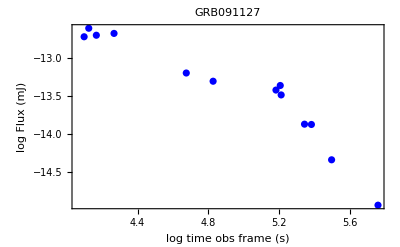

4.6

5.8

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 9

----------------------------------------------

best fit parameters: {F→-14.0764,T→5.45886,α→3.03421,t→27806.3}

theirs errors: {0.743608,0.257742,1.3607,34276.9}

confidence intervals: {{-14.8971,-13.2557},{5.1744,5.74332},{1.53245,4.53597},{-10024.,65636.6}}

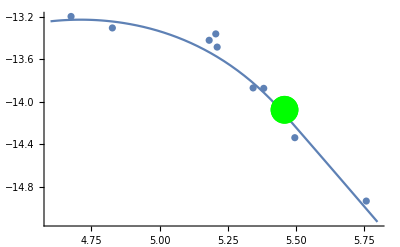

----------------------------------------------

GRB id afterglow has χ^2: 70.915 and  reduced χ^2: 11.8192 α: 0

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

0.229397 -0.0450677

0.241482 -0.0368254

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

0.222444 -0.197768

parameter | best fit |  confidency | interval
F | -14.0764 | (-14.1099 , | -13.9058)
T | 5.45886 | (5.44937 , | 5.5211)
α | 3.03421 | (2.76511 , | 3.33689)

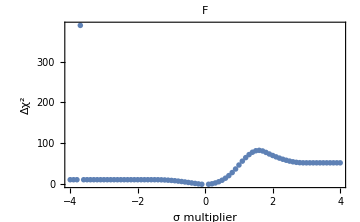
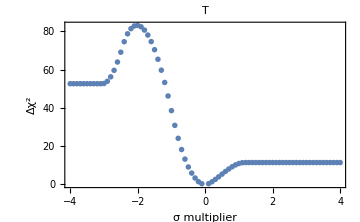
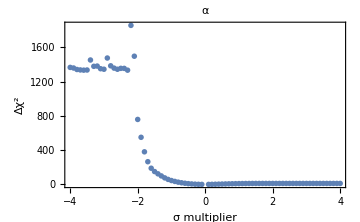

---------------------------------

```mathematica
Si["030429_R_flux.txt"](*Check again*)
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time obs frame (s)","log Flux (mJ)"},PlotLabel->"GRB091127"]

tt=4.6   (*start time of plateau, log scale*)
tf=5.8  (*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-13.37,5,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

```mathematica
(*Confirm Recover-dainotti approved*)
```

```mathematica
(*Confirm Recover-Dainotti approved*)
```

```mathematica
(*Approved, fit done by Dainotti*)
```

```mathematica
(*Approved Dainotti Checked*)
```

Part::partw: Part 29 of {{62.0908,5.00808×10^-12,8.54209×10^-13,8.54209×10^-13,R},{68.2381,5.30107×10^-12,9.04184×10^-13,9.04184×10^-13,R},{82.4189,6.28694×10^-12,1.07234×10^-12,1.07234×10^-12,R},{94.9569,4.73128×10^-12,5.37998×10^-13,5.37998×10^-13,R},{114.69,5.30107×10^-12,6.02789×10^-13,6.02789×10^-13,R},{138.524,5.93946×10^-12,6.75382×10^-13,6.75382×10^-13,R},{167.311,5.00808×10^-12,8.54209×10^-13,8.54209×10^-13,R},{202.081,4.73128×10^-12,8.06997×10^-13,8.06997×10^-13,R},{232.822,5.30107×10^-12,6.02789×10^-13,6.02789×10^-13,R},«11»,{39949.6,1.39353×10^-13,1.58459×10^-14,1.58459×10^-14,R},{48251.7,1.39353×10^-13,7.92295×10^-15,7.92295×10^-15,R},{64048.9,7.89229×10^-14,2.69225×10^-14,2.69225×10^-14,R},{77359.1,7.45608×10^-14,1.27176×10^-14,1.27176×10^-14,R},{93435.2,3.00228×10^-14,1.02415×10^-14,1.02415×10^-14,R},{118307.,7.89229×10^-14,8.97439×10^-15,8.97439×10^-15,R},{157040.,6.65469×10^-14,1.13507×10^-14,1.13507×10^-14,R},{208453.,4.46979×10^-14,1.52475×10^-14,1.52475×10^-14,R}} does not exist.

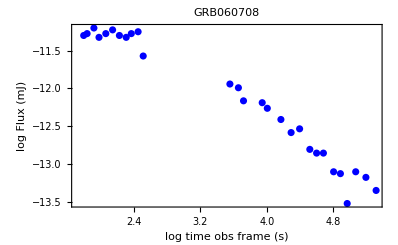

1.79

5.3

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 27

----------------------------------------------

best fit parameters: {F→-11.5644,T→3.11062,α→0.819888,t→-8.60239}

theirs errors: {0.0752042,0.121774,0.0336194,15.9016}

confidence intervals: {{-11.6408,-11.4879},{2.98684,3.23439},{0.785717,0.85406},{-24.7652,7.56043}}

!!!!!!!!!!!!!!!!!!! changing best fit parameters to: {F→-11.6007,T→3.15661,α→0.820982} with fixed ta->0

best fit parameters: {F→-11.6007,T→3.15661,α→0.820982}

theirs errors: {0.031247,0.0818329,0.0331034}

confidency intervals: {{-11.6324,-11.569},{3.07351,3.23971},{0.787366,0.854599}}

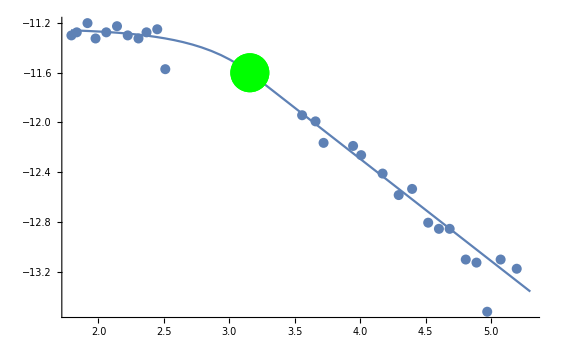

----------------------------------------------

GRB id afterglow has χ^2: 33.0487 and  reduced χ^2: 1.37703 α: 0.0917604

--------------testing-------------

---------------------------------

---------------------------------

0.962209 -0.739963

0.918817 -0.783237

0.95374 -0.751393

parameter | best fit |  confidency | interval
F | -11.6007 | (-11.6238 , | -11.5706)
T | 3.15661 | (3.09252 , | 3.2318)
α | 0.820982 | (0.796109 , | 0.852554)

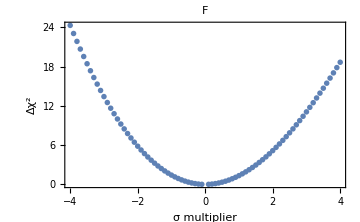
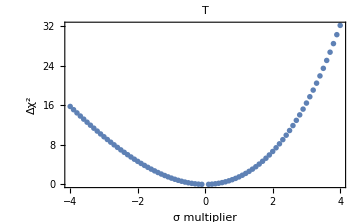
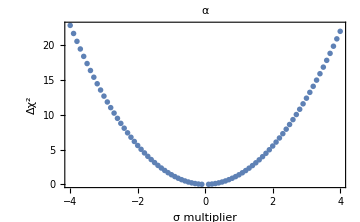

---------------------------------

```mathematica
Si["060708_Liang.txt"]
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time obs frame (s)","log Flux (mJ)"},PlotLabel->"GRB060708"]

tt=1.79 (*start time of plateau, log scale*)
tf=5.3  (*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-11.25,2.44,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

```mathematica
(*Approved fitting, Dainotti Checked*)
```

Part::partw: Part 42 of {{time,flux,flux_err1,band},{96.,1.98448×10^-11,2.40078×10^-12,R},{115.,1.22927×10^-10,1.68436×10^-11,R},{120.,1.56188×10^-10,2.01539×10^-11,R},{126.,2.02138×10^-10,1.60801×10^-11,R},{131.,1.96629×10^-10,2.37877×10^-11,R},{155.,9.94597×10^-11,1.28339×10^-11,R},{173.,6.04849×10^-11,6.32886×10^-12,R},{179.,5.72331×10^-11,4.06547×10^-12,R},«24»,{14328.6,2.04008×10^-13,1.79505×10^-14,R},{17005.3,1.9304×10^-13,1.53564×10^-14,R},{19535.9,1.59092×10^-13,1.66466×10^-14,R},{22239.4,1.19577×10^-13,1.63846×10^-14,R},{24875.4,1.04147×10^-13,1.25995×10^-14,R},{27325.7,9.49833×10^-14,1.30148×10^-14,R},{79545.,2.94881×10^-14,9.45969×10^-15,R},{103999.,2.7647×10^-14,8.86904×10^-15,R}} does not exist.

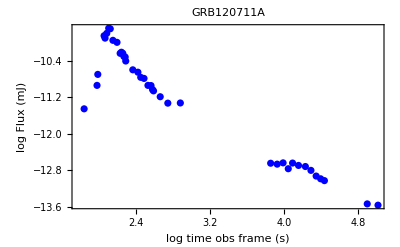

3

5

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 12

----------------------------------------------

best fit parameters: {F→-12.6826,T→4.30148,α→1.51971,t→6612.35}

theirs errors: {0.307662,0.161282,0.20856,4350.97}

confidence intervals: {{-13.0088,-12.3564},{4.13048,4.47247},{1.29859,1.74083},{1999.35,11225.4}}

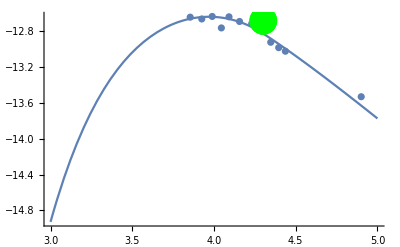

----------------------------------------------

GRB id afterglow has χ^2: 6.35541 and  reduced χ^2: 0.706157 α: 0.747089

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

0.659287 -0.521736

0.796296 -0.447681

1.28799 -1.08535

parameter | best fit |  confidency | interval
F | -12.6826 | (-12.8431 , | -12.4798)
T | 4.30148 | (4.22927 , | 4.4299)
α | 1.51971 | (1.29335 , | 1.78833)

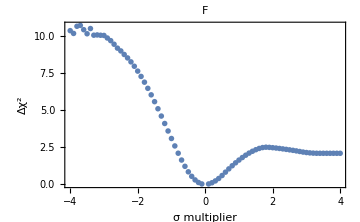
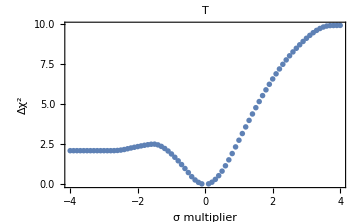
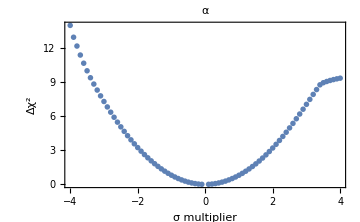

---------------------------------

```mathematica
Si["120711A_R_flux.txt"]
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time obs frame (s)","log Flux (mJ)"},PlotLabel->"GRB120711A"]

tt=3(*start time of plateau, log scale*)
tf=5 (*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-12.70,4.22,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

```mathematica
FINAL NOV30 102 SUCCESSFUL FITS MARCH 1
```

### 060904b (Approved by Dainotti)

Part::partw: Part 28 of {{time,flux,flux_err,band},{32.2,1.60564×10^-12,1.60564×10^-12,R},{42.8,5.31676×10^-12,5.31676×10^-12,R},{65.2,1.60564×10^-12,1.60564×10^-12,R},«20»,{2134.2,9.41125×10^-13,1.58331×10^-13,R},{2320.8,7.97347×10^-13,1.21813×10^-13,R},{2509.8,1.10065×10^-12,2.01878×10^-13,R}} does not exist.

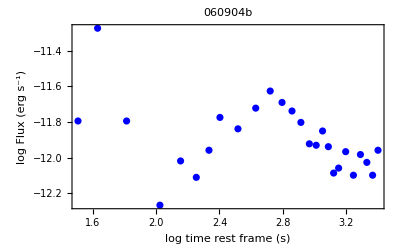

```mathematica
Si["060904b_tarot_ergs.txt"]
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"060904b"]
```

```mathematica
tt=2(*start time of plateau, log scale*)
tf=3.5(*end time of lightcurve, log scale*)
```

2

3.5

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 23

----------------------------------------------

best fit parameters: {F→-11.6066,T→2.86505,α→0.886483,t→264.895}

theirs errors: {0.193156,0.2088,0.119609,70.6487}

confidence intervals: {{-11.8038,-11.4093},{2.65183,3.07828},{0.764342,1.00862},{192.751,337.04}}

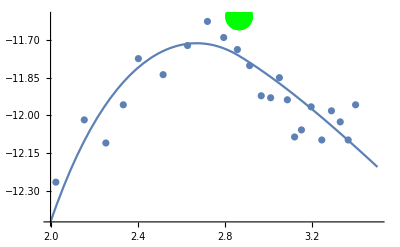

----------------------------------------------

GRB id afterglow has χ^2: 34.3147 and  reduced χ^2: 1.71574 α: 0.0176447

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

0.424705 -0.376834

0.415975 -0.236961

0.700357 -0.69237

parameter | best fit |  confidency | interval
F | -11.6066 | (-11.6794 , | -11.5246)
T | 2.86505 | (2.81558 , | 2.95191)
α | 0.886483 | (0.80367 , | 0.970252)

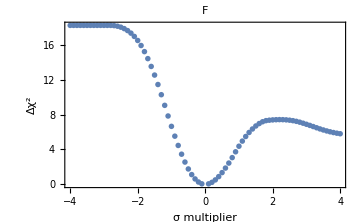
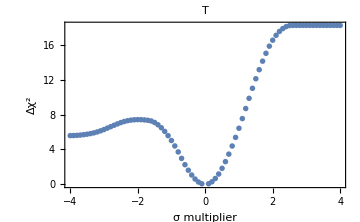
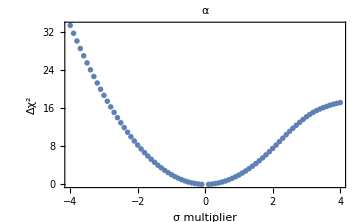

---------------------------------

```mathematica
Dzielenie[tt,tf]
fitowanie[-12.1,2.8,1.5,0,ΔF1,Part1,tt,tf]   (*fitting: y,x coords of turning point/end of plateau*)
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

### 081228 (approved by Dainotti)

Part::partw: Part 11 of {{time,flux,flux_err,band},{54.,2.11664×10^-12,2.11664×10^-12,R},{107.,1.33551×10^-12,1.33551×10^-12,R},{238.,5.31676×10^-13,5.31676×10^-13,R},{«1»},{«1»},{872.,7.07371×10^-14,«23»,R},{1380.,3.9962×10^-14,1.79859×10^-15,R},{1581.,3.54525×10^-14,1.59563×10^-15,R},{3308.,1.77684×10^-14,1.26215×10^-15,R}} does not exist.

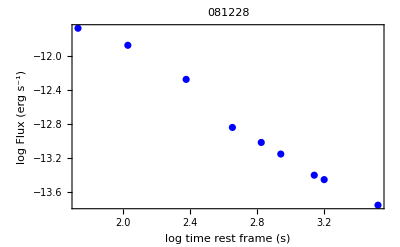

```mathematica
Liang["081228_tarot_ergs.txt"]
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"081228"]
```

```mathematica
tt=2.4(*start time of plateau, log scale*)
tf=3.5(*end time of lightcurve, log scale*)
```

2.4

3.5

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 5

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

----------------------------------------------

best fit parameters: {F→-13.0963,T→2.90579,α→1.25651,t→-0.0000713467}

theirs errors: {0.980464,0.480667,0.599035,790.274}

confidence intervals: {{-14.8797,-11.3128},{2.03146,3.78012},{0.166872,2.34615},{-1437.5,1437.5}}

!!!!!!!!!!!!!!!!!!! changing best fit parameters to: {F→-12.9876,T→2.80122,α→1.18347} with fixed ta->0

best fit parameters: {F→-12.9876,T→2.80122,α→1.18347}

theirs errors: {0.0375403,0.0362893,0.0274929}

confidency intervals: {{-13.0368,-12.9384},{2.75362,2.84881},{1.14742,1.21953}}

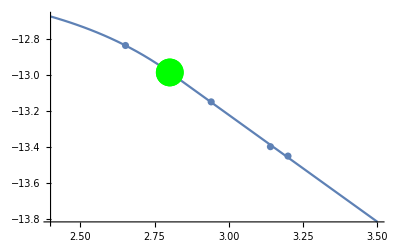

----------------------------------------------

GRB id afterglow has χ^2: 0.432726 and  reduced χ^2: 0.216363 α: 0.955701

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

2.03161 rightm

leftm -1.82874

2.25073 -2.12496

parameter | best fit |  confidency | interval
F | -12.9876 | (-12.9113 , | error)
T | 2.80122 | (2.73485 , | error)
α | 1.18347 | (1.12505 , | 1.24535)

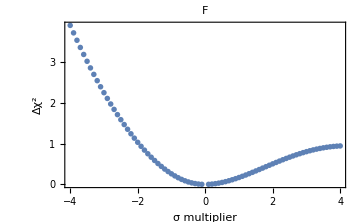
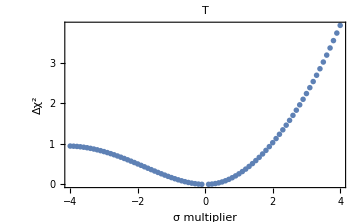
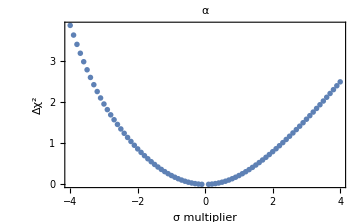

---------------------------------

```mathematica
Dzielenie[tt,tf]
fitowanie[-13,3,1.5,0,ΔF1,Part1,tt,tf]   (*fitting: y,x coords of turning point/end of plateau*)
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

### 130605a (approved by Dainotti)

Part::partw: Part 17 of {{time,flux,flux_err,band},{45.,1.39845×10^-11,1.22441×10^-13,R},{75.,1.33551×10^-11,1.22441×10^-13,R},{121.,1.11083×10^-11,1.22441×10^-13,R},«8»,{655.5,1.96629×10^-12,7.11226×10^-14,R},{933.3,8.58316×10^-13,5.35915×10^-14,R},{1158.3,5.51629×10^-13,1.29304×10^-13,R},{1705.,5.31676×10^-13,1.22441×10^-13,R}} does not exist.

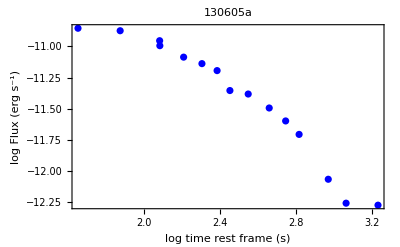

```mathematica
Si["130605a_tarot_ergs.txt"]
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"130605a"]
```

```mathematica
tt=2(*start time of plateau, log scale*)
tf=3.1(*end time of lightcurve, log scale*)
```

2

3.1

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 12

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

----------------------------------------------

best fit parameters: {F→-11.6623,T→2.7354,α→1.95938,t→-9.04584×10^-10}

theirs errors: {0.48534,0.269909,0.783346,56.6762}

confidence intervals: {{-12.1769,-11.1478},{2.44924,3.02157},{1.12886,2.7899},{-60.0894,60.0894}}

!!!!!!!!!!!!!!!!!!! changing best fit parameters to: {F→-11.2104,T→2.36883,α→1.14951} with fixed ta->0

best fit parameters: {F→-11.2104,T→2.36883,α→1.14951}

theirs errors: {0.0835729,0.0905884,0.118399}

confidency intervals: {{-11.2984,-11.1225},{2.27348,2.46417},{1.02489,1.27413}}

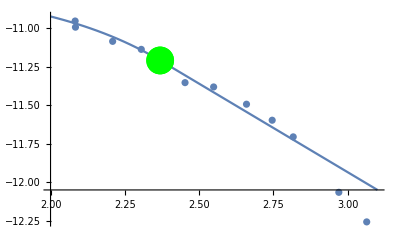

----------------------------------------------

GRB id afterglow has χ^2: 154.526 and  reduced χ^2: 17.1695 α: 0

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

0.351224 -0.137865

0.334045 -0.15451

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

0.352941 -0.144651

parameter | best fit |  confidency | interval
F | -11.2104 | (-11.222 , | -11.1811)
T | 2.36883 | (2.35483 , | 2.39909)
α | 1.14951 | (1.13238 , | 1.1913)

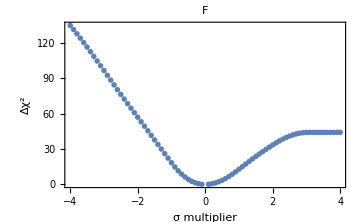
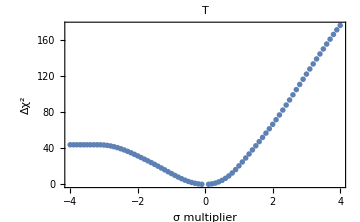
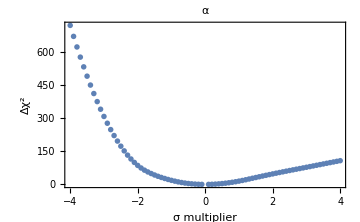

---------------------------------

```mathematica
Dzielenie[tt,tf]
fitowanie[-11.8,2.6,1.5,0,ΔF1,Part1,tt,tf]   (*fitting: y,x coords of turning point/end of plateau*)
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

KANN W07 ERGA

Part::partw: Part 95 of {{time,flux,flux_err,band},{22.9349,1.67834×10^-10,1.15519×10^-11,R},{39.0634,7.17873×10^-11,7.90679×10^-12,R},{47.1556,9.92712×10^-11,9.78109×10^-12,R},{55.4136,8.06727×10^-11,8.88545×10^-12,R},«42»,{1001.01,1.25509×10^-11,2.01538×10^-12,R},{1073.51,1.0604×10^-11,1.58659×10^-12,R},{1132.84,9.6214×10^-12,1.70053×10^-12,R},«44»} does not exist.

Part::partw: Part 5 of {22.9349,1.67834×10^-10,1.15519×10^-11,R} does not exist.

Part::partw: Part 6 of {22.9349,1.67834×10^-10,1.15519×10^-11,R} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

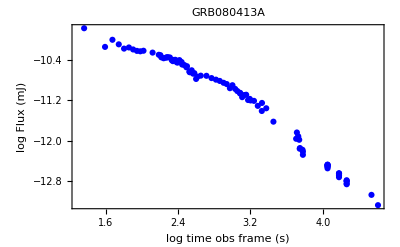

2

4.6

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 83

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

----------------------------------------------

best fit parameters: {F→-10.9122,T→2.95197,α→1.42515,t→-2.72468×10^-9}

theirs errors: {0.0737783,0.0595788,0.0260116,38.9943}

confidence intervals: {{-10.986,-10.8383},{2.89234,3.01159},{1.39912,1.45118},{-39.0238,39.0238}}

!!!!!!!!!!!!!!!!!!! changing best fit parameters to: {F→-10.8398,T→2.87788,α→1.40725} with fixed ta->0

best fit parameters: {F→-10.8398,T→2.87788,α→1.40725}

theirs errors: {0.0227745,0.0309327,0.0213552}

confidency intervals: {{-10.8626,-10.817},{2.84693,2.90883},{1.38588,1.42862}}

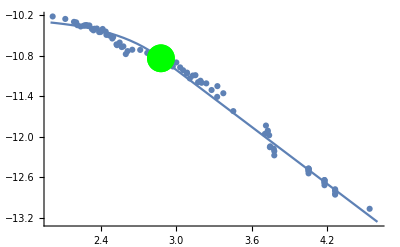

----------------------------------------------

GRB id afterglow has χ^2: 208.298 and  reduced χ^2: 2.60372 α: 0

--------------testing-------------

---------------------------------

---------------------------------

0.863822 -0.645524

0.834002 -0.65023

0.874478 -0.660529

parameter | best fit |  confidency | interval
F | -10.8398 | (-10.8545 , | -10.8201)
T | 2.87788 | (2.85777 , | 2.90368)
α | 1.40725 | (1.39314 , | 1.42592)

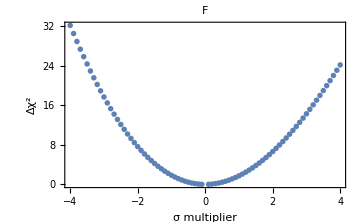
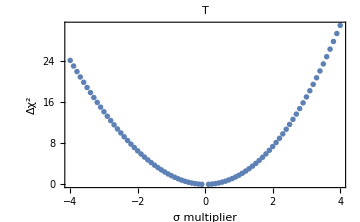
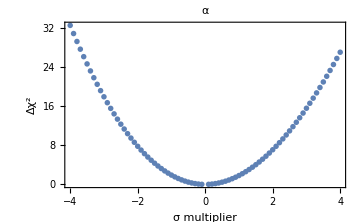

---------------------------------

```mathematica
Kann["080413A_Kann_mag_ergs.txt"](*Prompt emission (1.67,-9.77)*)(*Dainotti Approved*)
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time obs frame (s)","log Flux (mJ)"},PlotLabel->"GRB080413A"]

tt=2(*start time of plateau, log scale*)
tf=4.6(*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-10.68,2.69,3,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Part::partw: Part 197 of {{time,flux,flux_err,band},{25.2968,3.28433×10^-11,5.52544×10^-12,R},{78.9693,3.31472×10^-11,1.86863×10^-12,R},{88.994,2.62088×10^-11,1.59112×10^-12,R},{99.015,1.91094×10^-11,1.32468×10^-12,R},«42»,{6061.84,1.21818×10^-12,1.07187×10^-13,R},{6082.98,1.22025×10^-12,4.91716×10^-13,R},{6173.71,1.15647×10^-12,1.01757×10^-13,R},«146»} does not exist.

Part::partw: Part 5 of {25.2968,3.28433×10^-11,5.52544×10^-12,R} does not exist.

Part::partw: Part 6 of {25.2968,3.28433×10^-11,5.52544×10^-12,R} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

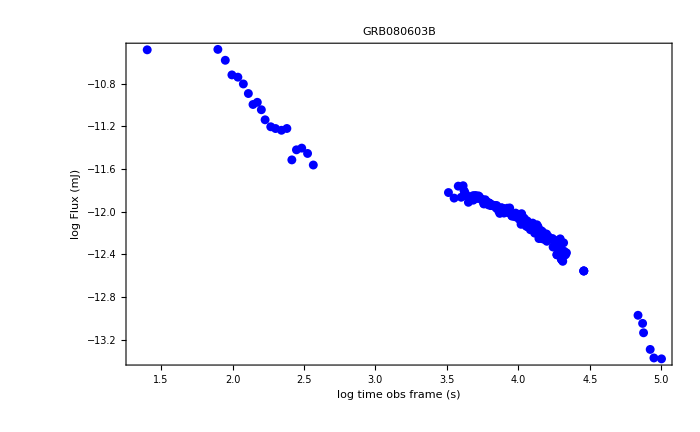

2.55

5

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 175

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

----------------------------------------------

best fit parameters: {F→-12.2783,T→4.22651,α→1.2999,t→-5.65386×10^-9}

theirs errors: {0.0183816,0.0163541,0.0287376,337.787}

confidence intervals: {{-12.2966,-12.26},{4.2102,4.24282},{1.27124,1.32857},{-336.894,336.894}}

!!!!!!!!!!!!!!!!!!! changing best fit parameters to: {F→-12.2511,T→4.19971,α→1.26607} with fixed ta->0

best fit parameters: {F→-12.2511,T→4.19971,α→1.26607}

theirs errors: {0.0151557,0.0148501,0.0269502}

confidency intervals: {{-12.2663,-12.236},{4.18489,4.21452},{1.23919,1.29295}}

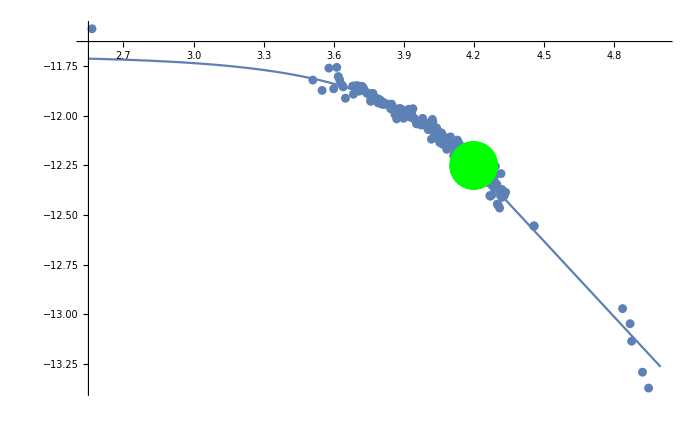

----------------------------------------------

GRB id afterglow has χ^2: 178.801 and  reduced χ^2: 1.03954 α: 0.344352

--------------testing-------------

---------------------------------

---------------------------------

1.13536 -0.941876

1.12704 -0.942452

1.16985 -0.945872

parameter | best fit |  confidency | interval
F | -12.2511 | (-12.2654 , | -12.2339)
T | 4.19971 | (4.18571 , | 4.21644)
α | 1.26607 | (1.24058 , | 1.2976)

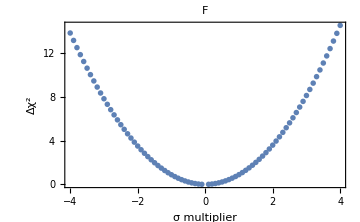
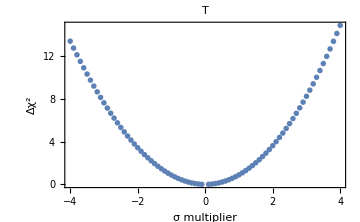
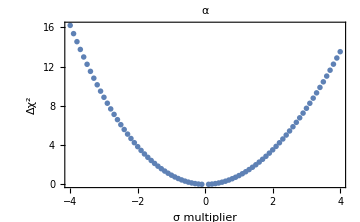

---------------------------------

```mathematica
Kann["080603B_Kann_mag_ergs.txt"](*Dainotti Approved*)
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time obs frame (s)","log Flux (mJ)"},PlotLabel->"GRB080603B"]

tt=2.55   (*start time of plateau, log scale*)
tf=5 (*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-12.27,4.26,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

```mathematica
10^1.66
```

45.7088

Part::partw: Part 147 of {{time,flux,flux_err,band},{49.5899,2.20621×10^-11,1.94123×10^-12,R},{44.6888,2.14609×10^-11,2.06777×10^-12,R},{47.2894,2.0495×10^-11,1.9747×10^-12,R},{59.2916,1.93931×10^-11,2.0292×10^-12,R},«42»,{562.006,6.8058×10^-13,2.1405×10^-13,R},{654.192,6.78652×10^-13,3.64863×10^-14,R},{751.613,6.38532×10^-13,1.75032×10^-14,R},«96»} does not exist.

Part::partw: Part 5 of {49.5899,2.20621×10^-11,1.94123×10^-12,R} does not exist.

Part::partw: Part 6 of {49.5899,2.20621×10^-11,1.94123×10^-12,R} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

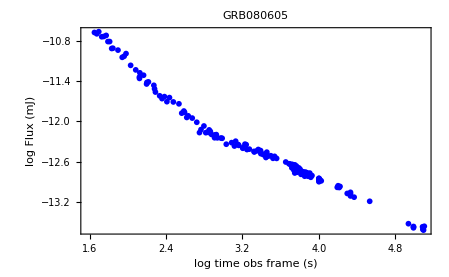

3

5.1

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 89

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

----------------------------------------------

best fit parameters: {F→-12.6326,T→3.69746,α→0.747852,t→-1.44166×10^-9}

theirs errors: {0.0390383,0.0470261,0.0176816,130.364}

confidence intervals: {{-12.6716,-12.5935},{3.65042,3.7445},{0.730165,0.765539},{-130.405,130.405}}

!!!!!!!!!!!!!!!!!!! changing best fit parameters to: {F→-12.5404,T→3.52993,α→0.680096} with fixed ta->0

best fit parameters: {F→-12.5404,T→3.52993,α→0.680096}

theirs errors: {0.0121994,0.0232376,0.0106894}

confidency intervals: {{-12.5526,-12.5282},{3.50669,3.55317},{0.669404,0.690788}}

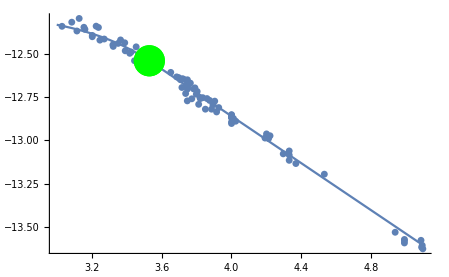

----------------------------------------------

GRB id afterglow has χ^2: 115.703 and  reduced χ^2: 1.34538 α: 0.0165583

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

1.04838 -0.964692

1.15675 -0.845333

1.05484 -0.857255

parameter | best fit |  confidency | interval
F | -12.5404 | (-12.5522 , | -12.5276)
T | 3.52993 | (3.51029 , | 3.55681)
α | 0.680096 | (0.670933 , | 0.691372)

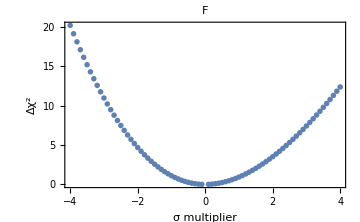
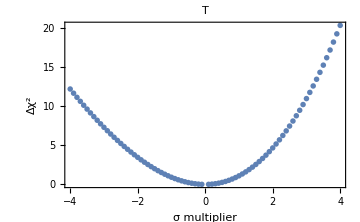
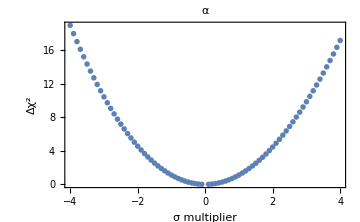

---------------------------------

```mathematica
Kann["080605_Kann_mag_ergs.txt"] (*Dainotti Approved*)
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time obs frame (s)","log Flux (mJ)"},PlotLabel->"GRB080605"]

tt=3(*start time of plateau, log scale*)
tf=5.1(*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-12.81,3.9,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

```mathematica
10^1.65
```

44.6684

Part::partw: Part 122 of {{time,flux,flux_err,band},{148.436,7.73648×10^-12,1.12127×10^-12,R},{170.848,1.89159×10^-11,9.83972×10^-13,R},{180.859,2.26374×10^-11,1.11818×10^-12,R},{190.87,2.9109×10^-11,1.38683×10^-12,R},«42»,{811.974,7.19759×10^-11,3.49222×10^-12,R},{821.855,7.65574×10^-11,3.71451×10^-12,R},{841.301,6.451×10^-11,2.56204×10^-12,R},«71»} does not exist.

Part::partw: Part 5 of {148.436,7.73648×10^-12,1.12127×10^-12,R} does not exist.

Part::partw: Part 6 of {148.436,7.73648×10^-12,1.12127×10^-12,R} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

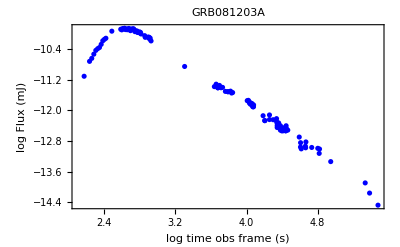

2.5

5.5

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 108

----------------------------------------------

best fit parameters: {F→-9.85813,T→2.83705,α→1.66673,t→265.377}

theirs errors: {0.100247,0.0441713,0.0262143,58.8474}

confidence intervals: {{-9.9583,-9.75796},{2.79292,2.88119},{1.64054,1.69293},{206.575,324.18}}

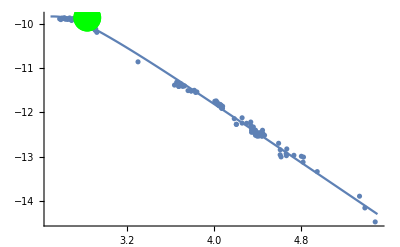

----------------------------------------------

GRB id afterglow has χ^2: 387.189 and  reduced χ^2: 3.68752 α: 0

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

0.402502 -0.215358

0.429477 -0.207076

0.542316 -0.341665

parameter | best fit |  confidency | interval
F | -9.85813 | (-9.87971 , | -9.81778)
T | 2.83705 | (2.82791 , | 2.85603)
α | 1.66673 | (1.65778 , | 1.68095)

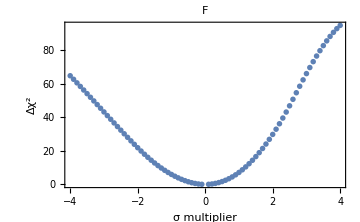
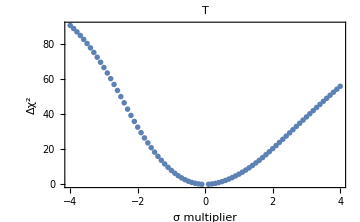
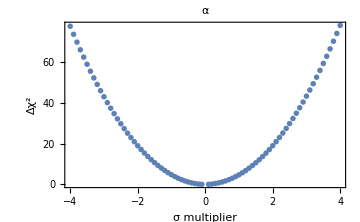

---------------------------------

```mathematica
Kann["081203A_Kann_mag_ergs.txt"](*Dainotti-Approved*)
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time obs frame (s)","log Flux (mJ)"},PlotLabel->"GRB081203A"]

tt=2.5  (*start time of plateau, log scale*)
tf=5.5(*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-10.18,2.92,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Part::partw: Part 102 of {{time,flux,flux_err,band},{75.8554,2.28964×10^-11,2.20608×10^-12,R},{81.8389,2.02007×10^-11,1.97995×10^-12,R},{100.11,1.98101×10^-11,1.04778×10^-12,R},{110.129,2.06865×10^-11,1.09413×10^-12,R},«42»,{5602.53,9.52461×10^-13,1.62424×10^-13,R},{5776.56,6.90493×10^-13,3.71229×10^-14,R},{5776.56,6.59416×10^-13,6.35351×10^-14,R},«51»} does not exist.

Part::partw: Part 5 of {75.8554,2.28964×10^-11,2.20608×10^-12,R} does not exist.

Part::partw: Part 6 of {75.8554,2.28964×10^-11,2.20608×10^-12,R} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

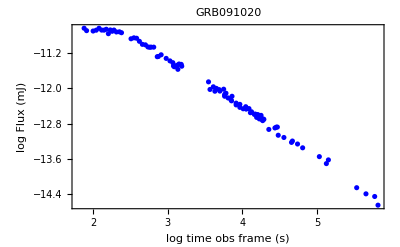

1.85

5.81

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 99

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

----------------------------------------------

best fit parameters: {F→-10.8705,T→2.58947,α→1.08875,t→35.3701}

theirs errors: {0.0493733,0.0419435,0.00706057,10.5031}

confidence intervals: {{-10.9198,-10.8211},{2.54754,2.6314},{1.08169,1.09581},{24.8703,45.87}}

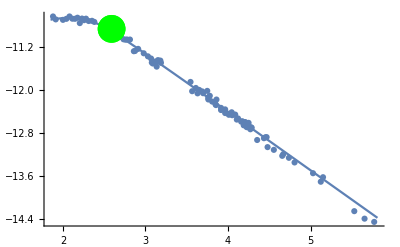

----------------------------------------------

GRB id afterglow has χ^2: 83.8835 and  reduced χ^2: 0.873786 α: 0.810692

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

1.08555 -0.933336

1.14618 -0.88143

1.14269 -0.938759

parameter | best fit |  confidency | interval
F | -10.8705 | (-10.9166 , | -10.8169)
T | 2.58947 | (2.5525 , | 2.63755)
α | 1.08875 | (1.08212 , | 1.09682)

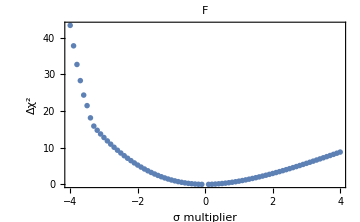
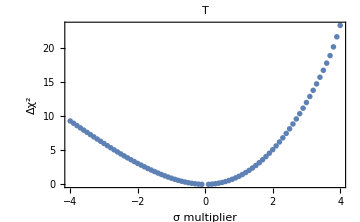
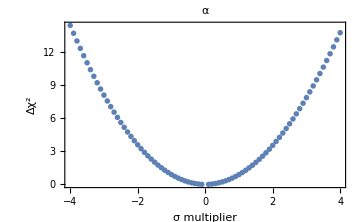

---------------------------------

```mathematica
Kann["091020_Kann_mag_ergs.txt"](*Dainotti Approved*)
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time obs frame (s)","log Flux (mJ)"},PlotLabel->"GRB091020"]

tt=1.85  (*start time of plateau, log scale*)
tf=5.81(*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-10.75,2.39,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Part::partw: Part 1033 of {{time,flux,flux_err,band},{81.8524,1.80758×10^-12,6.73647×10^-13,R},{123.495,3.46769×10^-12,8.45808×10^-13,R},{167.418,6.10446×10^-12,3.83647×10^-13,R},{202.101,1.88612×10^-12,1.87542×10^-13,R},«42»,{1072.7,1.1719×10^-12,3.03861×10^-14,R},{1072.7,1.13662×10^-12,2.10257×10^-14,R},{1072.7,1.12246×10^-12,3.13404×10^-14,R},«982»} does not exist.

Part::partw: Part 5 of {81.8524,1.80758×10^-12,6.73647×10^-13,R} does not exist.

Part::partw: Part 6 of {81.8524,1.80758×10^-12,6.73647×10^-13,R} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

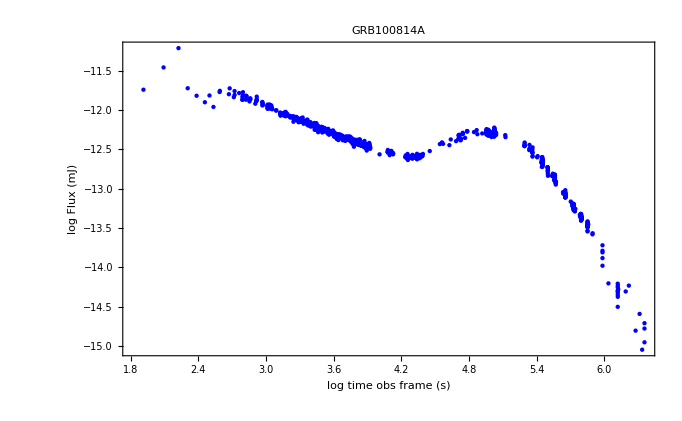

4.2

6.4

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 513

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

----------------------------------------------

best fit parameters: {F→-12.9168,T→5.59489,α→2.25952,t→27768.3}

theirs errors: {0.0268128,0.0131638,0.0530886,379.077}

confidence intervals: {{-12.9435,-12.8901},{5.58178,5.60799},{2.20668,2.31237},{27390.9,28145.6}}

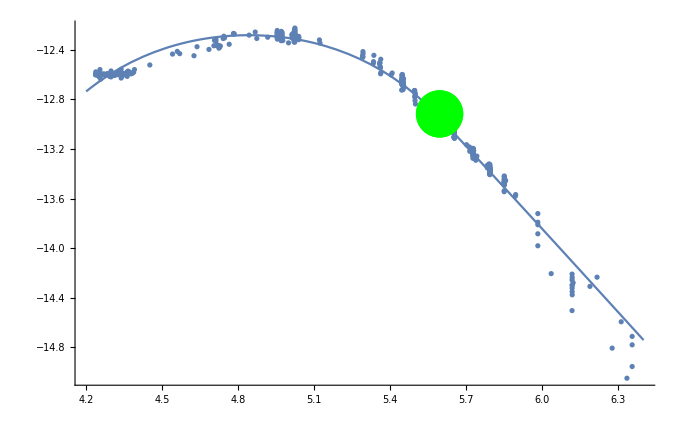

----------------------------------------------

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

GRB id afterglow has χ^2: 15494.6 and  reduced χ^2: 30.3816 α: 0

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

0.238247 -0.0406491

0.240434 -0.0388803

0.239198 -0.0364949

parameter | best fit |  confidency | interval
F | -12.9168 | (-12.9179 , | -12.9104)
T | 5.59489 | (5.59438 , | 5.59805)
α | 2.25952 | (2.25759 , | 2.27222)

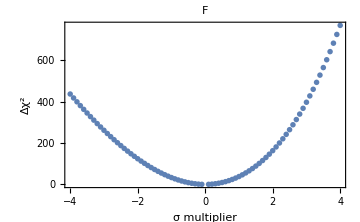
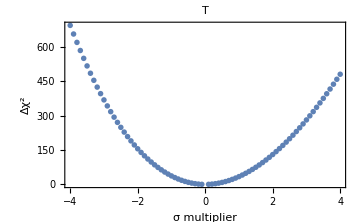
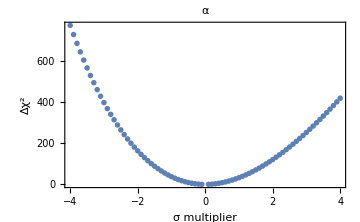

---------------------------------

```mathematica
Kann["100814A_Kann_mag_ergs.txt"](*Dainotti Approved*)(*Prompt emission at (2.22,-11.22)*)
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time obs frame (s)","log Flux (mJ)"},PlotLabel->"GRB100814A"]

tt=4.20 (*start time of plateau, log scale*)
tf=6.4(*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-12.37,5.27,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Part::partw: Part 308 of {{time,flux,flux_err,band},{30.0963,8.04725×10^-12,7.0807×10^-13,R},{74.,3.12982×10^-12,2.7539×10^-13,R},{77.,4.16408×10^-12,2.9579×10^-13,R},{81.,4.08808×10^-12,2.90391×10^-13,R},«41»,{422.,2.37839×10^-11,1.68946×10^-12,R},{428.,2.37819×10^-11,4.12555×10^-13,R},{437.,2.31357×10^-11,6.30513×10^-13,R},{442.,2.22989×10^-11,1.77389×10^-12,R},«257»} does not exist.

Part::partw: Part 5 of {30.0963,8.04725×10^-12,7.0807×10^-13,R} does not exist.

Part::partw: Part 6 of {30.0963,8.04725×10^-12,7.0807×10^-13,R} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

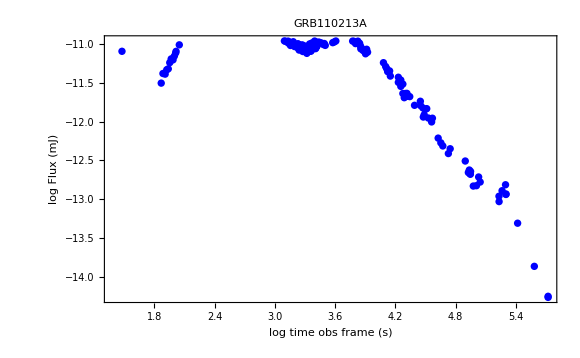

3.2

6

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 150

----------------------------------------------

best fit parameters: {F→-11.5304,T→4.36285,α→1.91037,t→1282.59}

theirs errors: {0.0418697,0.0389719,0.0659569,82.762}

confidence intervals: {{-11.5722,-11.4886},{4.32396,4.40174},{1.84456,1.97619},{1200.01,1365.18}}

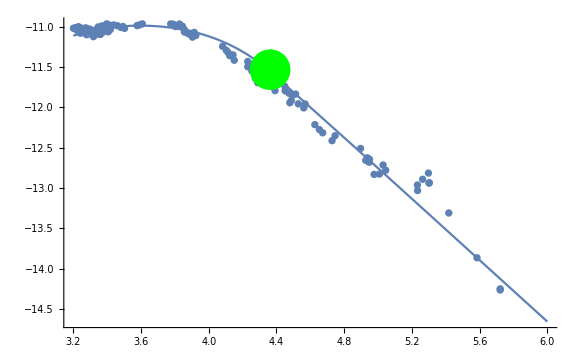

----------------------------------------------

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

GRB id afterglow has χ^2: 6840.06 and  reduced χ^2: 46.531 α: 0

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

0.265677 -0.0663803

0.266872 -0.0661134

0.265355 -0.0643217

parameter | best fit |  confidency | interval
F | -11.5304 | (-11.5332 , | -11.5193)
T | 4.36285 | (4.36027 , | 4.37325)
α | 1.91037 | (1.90613 , | 1.92787)

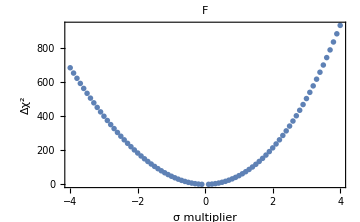
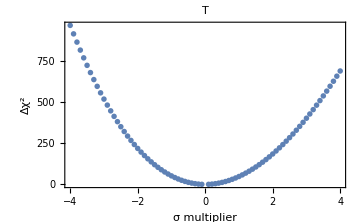
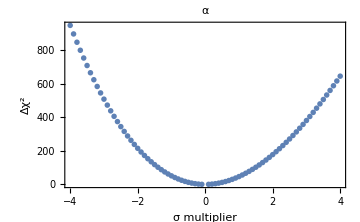

---------------------------------

```mathematica
Kann["110213A_Kann_mag_ergs.txt"](*Dainotti Approved*)(*Cut flare at -10.96*)
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time obs frame (s)","log Flux (mJ)"},PlotLabel->"GRB110213A"]

tt=3.2  (*start time of plateau, log scale*)
tf=6(*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-10.82,3.7,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Part::partw: Part 53 of {{time,flux,flux_err,band},{85.6224,3.94864×10^-11,5.41048×10^-12,R},{104.371,2.88435×10^-11,2.53791×10^-12,R},{114.394,2.27011×10^-11,2.18726×10^-12,R},{124.416,2.22868×10^-11,2.14734×10^-12,R},«42»,{335529.,1.1589×10^-13,4.47613×10^-14,R},{388473.,1.04147×10^-13,3.02474×10^-15,R},{391335.,9.91853×10^-14,3.14637×10^-15,R},«2»} does not exist.

Part::partw: Part 5 of {85.6224,3.94864×10^-11,5.41048×10^-12,R} does not exist.

Part::partw: Part 6 of {85.6224,3.94864×10^-11,5.41048×10^-12,R} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

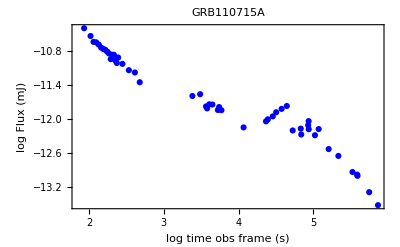

3.3

5.88

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 31

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

----------------------------------------------

best fit parameters: {F→-12.484,T→5.2529,α→1.55347,t→-1.87908×10^-10}

theirs errors: {0.0909016,0.0811207,0.123994,672.484}

confidence intervals: {{-12.5761,-12.3919},{5.17072,5.33509},{1.42785,1.67909},{-681.301,681.301}}

!!!!!!!!!!!!!!!!!!! changing best fit parameters to: {F→-12.3814,T→5.16243,α→1.46942} with fixed ta->0

best fit parameters: {F→-12.3814,T→5.16243,α→1.46942}

theirs errors: {0.0685837,0.0726866,0.103069}

confidency intervals: {{-12.4508,-12.312},{5.08884,5.23602},{1.36507,1.57377}}

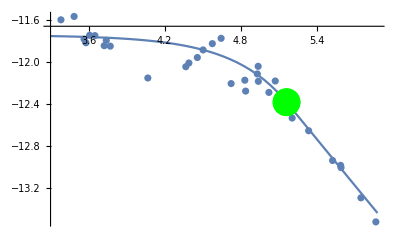

----------------------------------------------

GRB id afterglow has χ^2: 106.468 and  reduced χ^2: 3.80244 α: 0

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

0.646817 -0.446313

0.630043 -0.458498

0.663848 -0.438555

parameter | best fit |  confidency | interval
F | -12.3814 | (-12.412 , | -12.337)
T | 5.16243 | (5.1291 , | 5.20822)
α | 1.46942 | (1.42422 , | 1.53784)

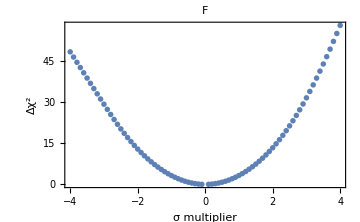
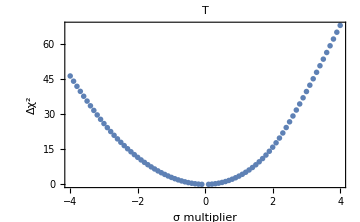
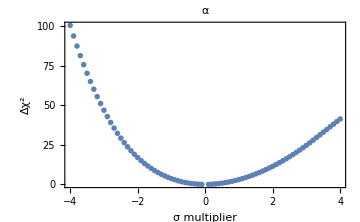

---------------------------------

```mathematica
Kann["110715A_Kann_mag_ergs.txt"](*Dainotti-Approved*)
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time obs frame (s)","log Flux (mJ)"},PlotLabel->"GRB110715A"]

tt=3.3  (*start time of plateau, log scale*)
tf=5.88(*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-12.32,5.04,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Part::partw: Part 72 of {{time,flux,flux_err,band},{25.5758,5.1576×10^-12,1.24516×10^-12,R},{32.187,5.1576×10^-12,1.24516×10^-12,R},{44.587,5.1576×10^-12,8.67694×10^-13,R},{65.0498,5.35534×10^-12,4.66712×10^-13,R},«42»,{3058.05,1.57442×10^-13,9.83033×10^-15,R},{3271.06,1.93173×10^-13,1.37218×10^-14,R},{3382.07,1.6948×10^-13,9.11174×10^-15,R},«21»} does not exist.

Part::partw: Part 5 of {25.5758,5.1576×10^-12,1.24516×10^-12,R} does not exist.

Part::partw: Part 6 of {25.5758,5.1576×10^-12,1.24516×10^-12,R} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

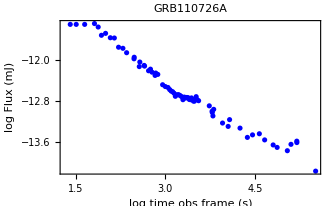

3.2

5.51

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 36

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

----------------------------------------------

best fit parameters: {F→-12.8369,T→3.531,α→0.705688,t→-1.23968×10^-9}

theirs errors: {0.256993,0.264822,0.0813284,876.328}

confidence intervals: {{-13.0965,-12.5773},{3.26349,3.79851},{0.623534,0.787842},{-885.225,885.225}}

!!!!!!!!!!!!!!!!!!! changing best fit parameters to: {F→-12.8547,T→3.5628,α→0.717409} with fixed ta->0

best fit parameters: {F→-12.8547,T→3.5628,α→0.717409}

theirs errors: {0.0471523,0.0841777,0.0422127}

confidency intervals: {{-12.9023,-12.8071},{3.47781,3.64779},{0.674788,0.760029}}

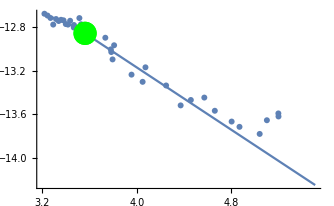

----------------------------------------------

GRB id afterglow has χ^2: 73.3638 and  reduced χ^2: 2.22315 α: 0.0000343648

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

0.560408 -0.336646

0.546961 -0.365739

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

0.655892 -0.437283

parameter | best fit |  confidency | interval
F | -12.8547 | (-12.8706 , | -12.8283)
T | 3.5628 | (3.53202 , | 3.60884)
α | 0.717409 | (0.69895 , | 0.745096)

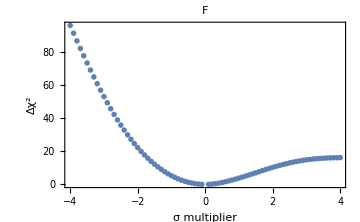
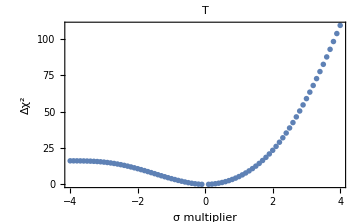
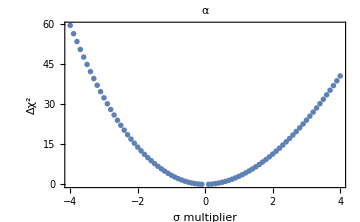

---------------------------------

```mathematica
Kann["110726A_Kann_mag_ergs.txt"](*Dainotti Approved*)
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time obs frame (s)","log Flux (mJ)"},PlotLabel->"GRB110726A"]

tt=3.2  (*start time of plateau, log scale*)
tf=5.51(*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-12.92,3.8,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Part::partw: Part 85 of {{61.8365,1.47044×10^-10,7.90548×10^-12,8.35465×10^-12,0.66,2.83},{79.8422,8.69853×10^-11,5.43119×10^-12,5.79289×10^-12,0.66,2.83},{89.8646,8.08065×10^-11,5.04539×10^-12,5.3814×10^-12,0.66,2.83},{99.8784,7.16879×10^-11,4.47605×10^-12,4.77414×10^-12,0.66,2.83},{109.884,6.01791×10^-11,3.75747×10^-12,4.0077×10^-12,0.66,2.83},{119.897,5.09854×10^-11,3.62168×10^-12,3.89861×10^-12,0.66,2.83},«40»,{1293.99,1.67726×10^-12,2.06444×10^-13,2.35421×10^-13,0.66,2.83},{1358.01,1.62136×10^-12,2.06097×10^-13,2.3611×10^-13,0.66,2.83},{1421.99,1.66051×10^-12,2.07999×10^-13,2.37784×10^-13,0.66,2.83},{1506.01,1.45757×10^-12,2.0029×10^-13,2.32196×10^-13,0.66,2.83},«34»} does not exist.

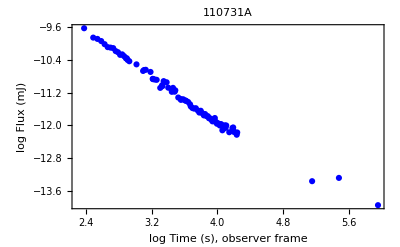

2.48

5.4

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 81

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

----------------------------------------------

best fit parameters: {F→-12.222,T→4.09843,α→4.13692,t→-5.07219×10^-9}

theirs errors: {0.417442,0.122696,0.865752,474.09}

confidence intervals: {{-12.6398,-11.8041},{3.97563,4.22124},{3.27037,5.00347},{-474.526,474.526}}

!!!!!!!!!!!!!!!!!!! changing best fit parameters to: {F→-10.0635,T→2.66711,α→1.40608} with fixed ta->0

best fit parameters: {F→-10.0635,T→2.66711,α→1.40608}

theirs errors: {0.0468479,0.0360832,0.00925101}

confidency intervals: {{-10.1103,-10.0166},{2.631,2.70323},{1.39682,1.41534}}

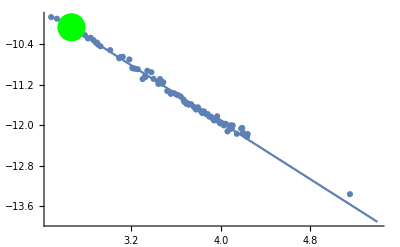

----------------------------------------------

GRB id afterglow has χ^2: 36.3607 and  reduced χ^2: 0.466163 α: 0.99999

--------------testing-------------

---------------------------------

---------------------------------

1.51698 -1.82362

2.0581 -1.49099

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

1.51952 -1.42545

parameter | best fit |  confidency | interval
F | -10.0635 | (-10.1489 , | -9.99239)
T | 2.66711 | (2.61331 , | 2.74138)
α | 1.40608 | (1.39289 , | 1.42014)

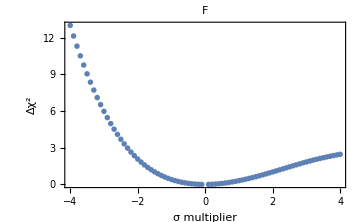
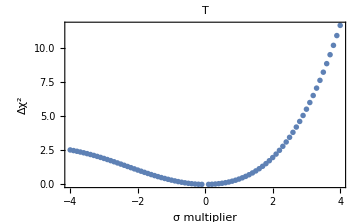
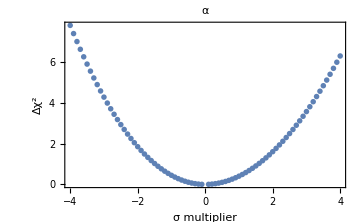

---------------------------------

```mathematica
Wczytywanie["110731A_block1_ergs.txt"] 
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log Time (s), observer frame","log Flux (mJ)"},PlotLabel->"110731A"]

tt=2.48  (*start time of plateau, log scale*)
tf=5.4 (*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-13.35,5.1,1.5,0,ΔF1,Part1,tt,tf] (*flux at end of plateau, time at end of plateau*)
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Part::partw: Part 162 of {{time,flux,flux_err,band},{143.48,1.03993×10^-12,2.61886×10^-13,R},{153.485,9.94039×10^-13,2.53064×10^-13,R},{163.49,7.05023×10^-13,2.32304×10^-13,R},{173.495,8.97436×10^-13,2.43096×10^-13,R},«42»,{2079.13,2.51893×10^-12,1.78928×10^-13,R},{2104.08,2.33586×10^-12,6.36587×10^-14,R},{2233.66,2.23073×10^-12,4.58798×10^-13,R},«111»} does not exist.

Part::partw: Part 5 of {143.48,1.03993×10^-12,2.61886×10^-13,R} does not exist.

Part::partw: Part 6 of {143.48,1.03993×10^-12,2.61886×10^-13,R} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

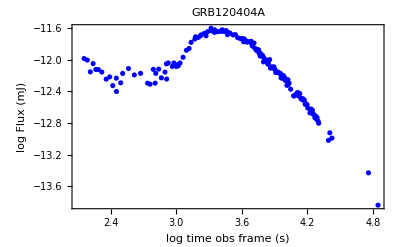

3.1

4.84

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 123

----------------------------------------------

best fit parameters: {F→-11.6472,T→3.70333,α→1.77697,t→2148.81}

theirs errors: {0.0344681,0.0156632,0.0144076,119.207}

confidence intervals: {{-11.6817,-11.6128},{3.68769,3.71897},{1.76258,1.79136},{2029.76,2267.85}}

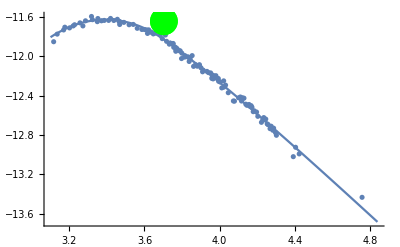

----------------------------------------------

GRB id afterglow has χ^2: 74.6882 and  reduced χ^2: 0.622402 α: 0.999666

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

1.58178 -1.51425

1.7303 -1.3575

1.32446 -1.28599

parameter | best fit |  confidency | interval
F | -11.6472 | (-11.6994 , | -11.5927)
T | 3.70333 | (3.68207 , | 3.73043)
α | 1.77697 | (1.75844 , | 1.79605)

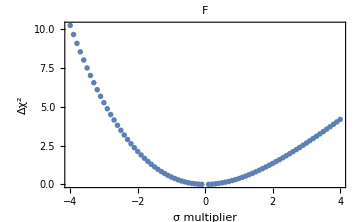
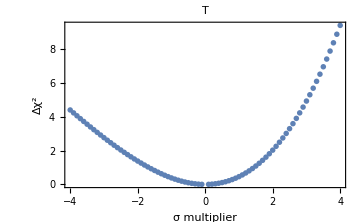
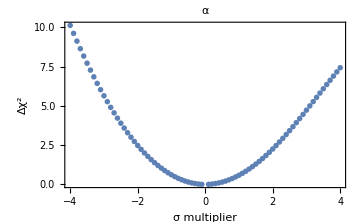

---------------------------------

```mathematica
Kann["120404A_Kann_mag_ergs.txt"](*Dainotti Approved*)
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time obs frame (s)","log Flux (mJ)"},PlotLabel->"GRB120404A"]

tt=3.1  (*start time of plateau, log scale*)
tf=4.84(*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-11.74,3.64,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

```mathematica
Kann["150910A_Kann_mag_ergs.txt"](*Dainotti Approved*)
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time obs frame (s)","log Flux (mJ)"},PlotLabel->"GRB150910A"]

tt=2.9  (*start time of plateau, log scale*)
tf=5.7(*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-11.31,3.26,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Part::partw: Part 203 of {{time,flux,flux_err,band},{318.402,3.96569×10^-13,8.84499×10^-14,R},{393.247,2.2989×10^-13,7.02578×10^-14,R},{433.176,1.79771×10^-13,6.99413×10^-14,R},{491.085,3.63118×10^-13,9.46776×10^-14,R},«42»,{2897.98,2.8906×10^-12,2.54341×10^-13,R},{2930.98,2.65001×10^-12,1.1927×10^-13,R},{2963.98,3.09035×10^-12,3.23359×10^-13,R},«152»} does not exist.

Part::partw: Part 5 of {318.402,3.96569×10^-13,8.84499×10^-14,R} does not exist.

Part::partw: Part 6 of {318.402,3.96569×10^-13,8.84499×10^-14,R} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

2.9

5.7

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 190

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

----------------------------------------------

best fit parameters: {F→-11.482,T→3.37855,α→1.23245,t→-3.57768×10^-9}

theirs errors: {0.109103,0.0694744,0.0194831,354.678}

confidence intervals: {{-11.5908,-11.3732},{3.30927,3.44782},{1.21302,1.25188},{-353.657,353.657}}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

!!!!!!!!!!!!!!!!!!! changing best fit parameters to: {F→-11.46,T→3.36387,α→1.239} with fixed ta->0

best fit parameters: {F→-11.46,T→3.36387,α→1.239}

theirs errors: {0.0280611,0.0249278,0.0082683}

confidency intervals: {{-11.4879,-11.432},{3.33902,3.38873},{1.23076,1.24725}}

-Graphics-

----------------------------------------------

GRB id afterglow has χ^2: 672.163 and  reduced χ^2: 3.59445 α: 0

--------------testing-------------

---------------------------------

---------------------------------

0.409519 -0.39614

0.400637 -0.213197

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

0.696 -0.494982

parameter | best fit |  confidency | interval
F | -11.46 | (-11.4711 , | -11.4485)
T | 3.36387 | (3.35856 , | 3.37386)
α | 1.239 | (1.23491 , | 1.24476)

-Graphics--Graphics--Graphics-

---------------------------------

```mathematica
Kann["121217A.txt"]
ListPlot[dane,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log Time (s), observer frame","log Flux (mJ)"},PlotLabel->"121217A"]

tt=3.24   (*start time of plateau, log scale*)
tf=5.54  (*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-12.3,3.54,1.67,0,ΔF1,Part1,tt,tf] (*flux at end of plateau, time at end of plateau*)
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Part::partw: Part 28 of {{1120.,4.72549×10^-13,1.74094×10^-14,1.74094×10^-14,R},{1229.,4.72549×10^-13,2.17617×10^-14,2.17617×10^-14,R},{1338.,4.04062×10^-13,1.48862×10^-14,1.48862×10^-14,R},{1447.,4.3097×10^-13,1.58775×10^-14,1.58775×10^-14,R},{1592.,6.40394×10^-13,1.17965×10^-14,1.17965×10^-14,R},{1787.,7.69924×10^-13,7.09126×10^-15,7.09126×10^-15,R},{1981.,7.42074×10^-13,1.36695×10^-14,1.36695×10^-14,R},{2173.,7.28529×10^-13,1.342×10^-14,1.342×10^-14,R},{2374.,6.89362×10^-13,1.26985×10^-14,1.26985×10^-14,R},«10»,{4518.,4.19225×10^-13,1.15836×10^-14,1.15836×10^-14,R},{4736.,3.85876×10^-13,1.77702×10^-14,1.77702×10^-14,R},{4736.,3.89446×10^-13,1.43477×10^-14,1.43477×10^-14,R},{74739.,4.90283×10^-14,2.25784×10^-15,2.25784×10^-15,R},{86363.,4.90283×10^-14,2.25784×10^-15,2.25784×10^-15,R},{88178.,4.11573×10^-14,1.51629×10^-15,1.51629×10^-15,R},{173620.,2.20012×10^-14,1.82375×10^-15,1.82375×10^-15,R},{347165.,1.15464×10^-14,1.27616×10^-15,1.27616×10^-15,R}} does not exist.

Part::partw: Part 6 of {1120.,4.72549×10^-13,1.74094×10^-14,1.74094×10^-14,R} does not exist.

Part::partw: Part 6 of {1229.,4.72549×10^-13,2.17617×10^-14,2.17617×10^-14,R} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

3.24

5.54

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

number of points included: 21

----------------------------------------------

best fit parameters: {F→-12.2295,T→3.47558,α→0.775179,t→66.1207}

theirs errors: {0.112489,0.0967395,0.0279074,300.139}

confidence intervals: {{-12.3447,-12.1143},{3.37648,3.57468},{0.746591,0.803768},{-241.344,373.585}}

-Graphics-

----------------------------------------------

GRB id afterglow has χ^2: 26.8556 and  reduced χ^2: 1.49198 α: 0.0683138

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

0.313834 -0.425984

0.626644 -0.24809

0.548799 -0.563926

parameter | best fit |  confidency | interval
F | -12.2295 | (-12.2774 , | -12.1942)
T | 3.47558 | (3.45158 , | 3.5362)
α | 0.775179 | (0.759442 , | 0.790495)

-Graphics--Graphics--Graphics-

---------------------------------

```mathematica
f[m_] = t*a*10^(-0.4*m);
D[f[m], m]
```

-0.921034 10^(-0.4 m) a t

```mathematica
0
```